# Laman Loopstrap

## Feynman Diagrams and Bootstrap for Four-Dimensional Holomorphic Theories

Code by Davide Gaiotto, Justin Kulp, and Matthew Yu.
https://github.com/TwistedQFTs/laman-loopstrap

```mathematica
Quit[];
```

```mathematica
(* Uncomment and run for improved emotional performance: *)
(*
SetOptions[SelectedNotebook[],StyleDefinitions->FileNameJoin[{$InstallationDirectory,"SystemFiles","FrontEnd","StyleSheets","Creative","PastelColor.nb"}]]
*)
```

This code is used to accompany the paper “Feynman Diagrams in Four-Dimensional Holomorphic Theories and the Operatope,” by Kasia Budzik, Davide Gaiotto, Justin Kulp, Jingxiang Wu, and Matthew Yu.
The code:
	1. Generates the Laman Graphs defined in Section 3 of the paper.
	2. Generates Sliding Graphs defined in Section 3 of the paper.
	3. Implements the Quadratic Relations for Feynman integrals in Equation (3.13) of the paper.
	4. Follows the examples in Section 4 o the paper.

## Code (Run me)

### Symbols and Notation

```mathematica
Clear[z,pz,mP,symp,lm,ZL,ZHold,λ]
```

```mathematica
(* Antisymmetry of edge variables *)
z[a_,b_]:=-z[b,a]/;a>b

(* Symbols for derivatives *)
pz[a_,b_]:=-pz[b,a]/;a>b
```

```mathematica
(*Makes 0^0 = 1*)
Attributes[mP]={Listable};
mP[0,0]=1;
mP[x_,y_]:=x^y;
```

```mathematica
(*SU(2) functions: symplectic product, a 2-vector of lambda's, a 2-vector of Z's*)
symp[{a_,b_},{c_,d_}]:=a d - b c
lm[index_]:={λ[index,1],λ[index,2]};
ZL[index_]:={ZHold[index,1],ZHold[index,2]};
```

```mathematica
(*Mathematical Functions*)
multiDotRight[tensor_,vector_,power_]:=Nest[Dot[#,vector]&,tensor,power]
mDR[t_,v_,p_]:=multiDotRight[t,v,p]
```

### Generating and Manipulating Laman Graphs

```mathematica
Clear[lamanSubgraphTestQ,lamanQ,hennMove1, hennMove2, hennApply]

(* Laman graph tests *)
lamanSubgraphTestQ[g_Graph]:=EdgeCount[g]≤2 VertexCount[g]-3;
lamanQ[g_Graph]:=(EdgeCount[g]==2 VertexCount[g]-3)&&(And@@Map[lamanSubgraphTestQ[Subgraph[g,#]]&][Subsets[VertexList[g],{2,VertexCount[g]}]])

(* Henneberg moves (naming convention from Wikipedia) *)
(* Apply Henneberg move that adds a vertex. *)
hennMove1[g_Graph,{v1_,v2_}]:=Module[
{new},
CanonicalGraph[EdgeAdd[VertexAdd[g,new],{v1<->new,v2<->new}]]
]
(* Henneberg move that splits an edge *)
hennMove2[g_Graph,{e_,v_}]:=Module[
{new},
CanonicalGraph[EdgeAdd[VertexAdd[EdgeDelete[g,e],new],{v<->new,List@@e[[1]]<->new,List@@e[[2]]<->new}]]
]
(* Apply Henneberg moves to a graph in all possible ways *)
hennApply[g_Graph]:=Module[
{
ver2=Subsets[VertexList[g],{2}],
edg=Select[Tuples[{EdgeList[g],VertexList[g]}],!MemberQ[List@@(#[[1]]),#[[2]]]&],
x,y
},
Union[Join[Table[hennMove1[g,x],{x,ver2}],Table[hennMove2[g,y],{y,edg}]]]
]
```

```mathematica
Clear[numSlots,numOuts, graphDiffQ]

(* Count locations which cannot contain a cubic interaction*)
numSlots[g_Graph]:=Module[{ver=VertexList[g],x},Select[ver,Length[IncidenceList[g,#]]>3&]]
(* Count locations which can produce an output when an interaction is inserted *)
numOuts[g_Graph]:=Module[{ver=VertexList[g],x},Select[ver,Length[IncidenceList[g,#]]<3&]]
(* Returns True if a graph can contribute to the differential *)
graphDiffQ[g_Graph]:=(Length[numSlots[g]]<=1)&&(Length[numOuts[g]]>1)
```

```mathematica
Clear[laman,unlaman,contractGraph]
laman[1]={};
laman[2]={Graph[{1<->2}]//CanonicalGraph};
laman[n_]:=(laman[n]=Union[Flatten[Thread[hennApply[laman[n-1]]]]])/;n>2

(* 1-Deformable graphs *)
unlaman[n_]:=Module[
{graph,edge},
Union[Flatten[Table[CanonicalGraph[EdgeDelete[graph,edge]],{graph,laman[n]},{edge,EdgeList[graph]}]]]
]
contractGraph[g_Graph]:=Module[
{
sub=Select[(Subgraph[g,#]&)/@Subsets[VertexList[g],{2,Length[VertexList[g]]}],lamanQ], (*Find all Laman subgraphs of input*)
x,y,graphs
},

graphs=Table[{x,VertexReplace[EdgeDelete[g,EdgeList[x]],Table[y->vertsToSymbol[VertexList[x]],{y,VertexList[x]}]]},{x,sub}];
Transpose[Select[graphs,lamanQ[#[[2]]]&]]
];
```

```mathematica
Clear[orderUndirectedGraph,relativeSignGraph,graphToCanonical,invertGraphIsomorphism]

(*What a strange problem to have: we perform lots of operations which check orders of edges..*)
orderUndirectedGraph[a_<->b_]:=Sort[a<->b]

(*Finds the sign of a graph relative to its canonical graph*)
relativeSignGraph[g_Graph]:=Module[{canonicalGraph,iso,eCanonical,eGraph},
canonicalGraph=CanonicalGraph[g];
iso=FindGraphIsomorphism[g,canonicalGraph];

eGraph=(EdgeList[g]/.iso)[[1]];
eCanonical=EdgeList[canonicalGraph];

Signature[Map[orderUndirectedGraph,eGraph]]/Signature[Map[orderUndirectedGraph,eCanonical]]
]

(*Eats a graph and outputs the graph, the canonical graph, an isomorphism to the canonical graph, and the inverse OF THAT ISOMORPHISM*)
graphToCanonical[g_Graph]:=Module[{canonicalGraph,iso},
canonicalGraph=CanonicalGraph[g];
iso=FindGraphIsomorphism[g,canonicalGraph][[1]]//Normal;
{g,canonicalGraph,iso,invertGraphIsomorphism[iso]}
]
invertGraphIsomorphism[iso_]:=Map[Reverse,iso];
```

```mathematica
Clear[vertsToSymbol,contractGraphSigned,displayGraph,displayContractions,displayContractionsTable]

vertsToSymbol[vertexList_]:=CirclePlus@@vertexList
contractGraphSigned[g_Graph]:=Module[
{
sub=Select[(Subgraph[g,#]&)/@Subsets[VertexList[g],{2,Length[VertexList[g]]}],lamanQ], (*Find all Laman subgraphs of input*)
x,y, graphs,complementSign,canonicalSigns
},

graphs=Table[{x,VertexReplace[EdgeDelete[g,EdgeList[x]],Table[y->vertsToSymbol[VertexList[x]],{y,VertexList[x]}]]},{x,sub}];
complementSign=Table[Join[EdgeList[x],Complement[EdgeList[g],EdgeList[x]]]//Signature,{x,sub}];
canonicalSigns=Table[Times@@Map[relativeSignGraph,x],{x,graphs}];

Select[Transpose[{complementSign*canonicalSigns,graphs}],(lamanQ[#[[2,2]]]&)]
];

(*For human readability: displays the graph, and also the quadratic relations*)
displayGraph[g_Graph]:=SetProperty[g,VertexLabels->"Name"]
displayContractions[contractionOutput_]:=Sum[contractionOutput[[i,1]]displayGraph[contractionOutput[[i,2,1]]]displayGraph[contractionOutput[[i,2,2]]],{i,1,Length[contractionOutput]}]
displayContractionsTable[contractionOutput_]:=Table[{x[[1]],{{x[[2,1]]//displayGraph,x[[2,1]]//VertexList,x[[2,1]]//EdgeList},{x[[2,2]]//displayGraph,x[[2,2]]//VertexList,x[[2,2]]//EdgeList}}//MatrixForm},{x,contractionOutput}]//TableForm

(*An alternative display shorthand*)
print[g_Graph]:=Graph[g,VertexLabels->Table[i->ToString[i],{i,VertexList[g]}]]
```

### Coefficient Extractor

```mathematica
Clear[seriesToLinEq]
```

```mathematica
(*https://mathematica.stackexchange.com/questions/83721/what-are-sparsearray-properties-how-and-when-should-they-be-used*)

(*
We have two polynomials with undetermined coefficients c[l,m,n,p,...] but we know that these polynomials must be equal aka f-g = 0.;
So we feed it as input with a variable list (variables defining the polynomials) and also the list of undetermined coefficients that we would like to figure out.;
*)
seriesToLinEq[poly_,varList_,coeffList_]:=Module[{coeffLHS,tableLHS,eqnTable,reducedTable},

(*Match powers in the polynomial inputs to extract just a list of *linear* equations in the unknowns c[l,m,n,p,...]*)
coeffLHS=CoefficientArrays[poly,varList];
tableLHS=Table[coeffLHS[[i]]["NonzeroValues"],{i,2,Length[coeffLHS]}];
tableLHS=DeleteCases[Flatten[tableLHS],0];

(*
We now have a series of linear(!) equations, we could just //Reduce these knowing the RHS = 0 for all of them.;
Since we know they are all linear, we will spare Mathematica the trouble and put them into matrix form ourselves.;
If an equation has dependency on a variable NOT in the varList, we remove it so that it doesn't break the solver.;
i.e. we hope that the problem is triangular, so that we can solve for the first n coefficients without having to look to equations involving more than the first n coefficients;
*)

(*This extracts the coefficients, the first sparse matrix are all equations not involving one of our variables, the second are linear equations involving our variable set.*)
eqnTable=CoefficientArrays[tableLHS,coeffList];
(*We delete all equations that involve our variables that also involve variables we did not specify.*)
reducedTable=Delete[eqnTable[[2]],eqnTable[[1]]["NonzeroPositions"]];

reducedTable.coeffList==0//Solve

]
```

### Function To Operator

```mathematica
Clear[functionToOperator,seriesToOperator,DeeHold]
```

```mathematica
(*
	Slot 1 - The function which will be an operator;
	Slot 2 - A list of lambdas which will be shifted, you DO NOT have to put all the lambdas involved in here, or all the variables. You only have to put variables in that you want to shift as a list. ;
	Slot 3 - You put it in the form {{-1,Z12},{2,Z34},{5,Z45}}.T his says take the first variable in lamList,aka lamList[[1]] and replace it in the function by lamList[[1]]->lamList-DeeHold[Z12]. Notice the minus sign because the first guy has -1 and DeeHold[Z12] because the first guy has Z12. Similarly,it shifts the variable lamList[[3]] by 5 DeeHold[Z45].;
	Slot 4 - A Depth list, it should also be the same length list as Slot 2 and Slot 3. It says in the variable DeeHold[...] expand that deep.
Slot 5 - The function g you want to hit.;
*)
functionToOperator[f_,lamList_,shiftList_,depthList_,g_]:=Module[{shiftTranspose,DeeShift,replacementList,expansionList,expansion,constantTerm},
shiftTranspose=Transpose[shiftList];
DeeShift=shiftTranspose[[1]]*Map[DeeHold,shiftTranspose[[2]]];

replacementList=Table[lamList[[i]]->(lamList+DeeShift)[[i]],{i,1,Length[lamList]}];
expansionList=Table[{lamList[[i]],0,depthList[[i]]},{i,1,Length[lamList]}];

expansion=(Normal[(Series[f,##]&)@@expansionList]/.replacementList)//Expand;
constantTerm=Normal[(Series[f,##]&)@@Table[{lamList[[i]],0,depthList[[i]]},{i,1,Length[lamList]}]]//Expand;

(expansion/.(DeeHold[zz_]^(m_.):>D[g,{zz,m}]))+constantTerm(g-1)//Expand
]
```

```mathematica
seriesToOperator[f_,lamList_,shiftList_,g_]:=Module[{shiftTranspose,DeeShift,replacementList,expansion,constantTerm,iHold},
shiftTranspose=Transpose[shiftList];
DeeShift=shiftTranspose[[1]]*Table[{DeeHold[shiftTranspose[[2,iHold,1]]],DeeHold[shiftTranspose[[2,iHold,2]]]},{iHold,1,Length[shiftTranspose[[2]]]}];

replacementList=Table[{lamList[[i,1]]->(lamList+DeeShift)[[i,1]],lamList[[i,2]]->(lamList+DeeShift)[[i,2]]},{i,1,Length[lamList]}]//Flatten;

expansion=f/.replacementList//Expand;
constantTerm=f/.(DeeHold[zz_]^(m_.):>0)//Expand;

(expansion/.(DeeHold[var_]^(m_.):>DeeHold[{var,m}])//.(DeeHold[list1_]DeeHold[list2_]:>DeeHold[Join[list1,list2]])/.(DeeHold[list_]:>DeeHold[ArrayReshape[list,{Length[list]/2,2}]])/.(DeeHold[list_]:>(D[g,##]&)@@list))+constantTerm(g-1)

]
```

### Quadratic Relation Generator

#### Implementing the quadratic relations in terms of I’s.

```mathematica
(* Find possible contractions. Outputs list of contractions, each with {subgraph, complement, complement with subgraph vertices identified to "new" vertex}*)
cut[g_Graph]:=Module[{sub=Select[(Subgraph[g,#]&)/@Subsets[VertexList[g],{2,Length[VertexList[g]]}],lamanQ],x,y},Select[Table[{x,EdgeDelete[g,EdgeList[x]],VertexReplace[EdgeDelete[g,EdgeList[x]],Table[y->new,{y,VertexList[x]}]]},{x,sub}],lamanQ[#[[3]]]&]]

(* vertex and edge variables for the first and second graph in the quadratic relations *)
(* The inputs a,b,c are the above {subgraph, complement, complement with subgraph vertices identified to "new" vertex} *)
ver1[{a_,b_,c_}]:=Table[l[i]+Total[ IncidenceList[b,i]/.u_<->v_:>If[u===i,pz[u,v],pz[v,u]]],{i,VertexList[a]}]
edge1[{a_,b_,c_}]:=Table[i/.u_<->v_:>z[u,v],{i,EdgeList[a]}]
ver2[{a_,b_,c_}]:=Table[l[i],{i,VertexList[c]}]/.l[new]->Total[Table[l[i],{i,VertexList[a]}]]
edge2[{a_,b_,c_}]:=Table[i/.u_<->v_:>z[u,v],{i,EdgeList[b]}]
```

```mathematica
(* Quadratic Relations Step 1: I1 represents the subgraph Feynman diagram acting on the contracted Feynman diagram I2 *)
quad[g_Graph]:=Module[{c=cut[g],i},Sum[Signature[EdgeList[g]]Signature[Join[EdgeList[i[[1]]],EdgeList[i[[2]]]]]I1[i[[1]],ver1[i],edge1[i]]I2[i[[3]],ver2[i],edge2[i]],{i,c}]]

(* Auxiliary function *)
canon[g_Graph]:=FindGraphIsomorphism[CanonicalGraph[g],g][[1]]

(* given non-canonical graph with vertex and edge variables in the same order as vertices and edges of the graph, outputs the canonical form of the graph, with appropriately ordered vertex and edge variables *)
canon[g_Graph,ver_,edge_]:={
CanonicalGraph[g],
Map[Part[ver,VertexIndex[g,#]]&][VertexList[CanonicalGraph[g]]/.canon[g]],Map[Signature[#]Signature[Part[EdgeList[g],EdgeIndex[g,#]]]Part[edge,EdgeIndex[g,#]]&][EdgeList[CanonicalGraph[g]]/.a_<->b_:>canon[g][a]<->canon[g][b]]
}

(* substitution which puts I1, I2 arguments in canonical order *)
canonsub={I1[a_,b_,c_]:>Signature[EdgeList[a]]Signature[EdgeList[CanonicalGraph[a]]/.canon[a]]I1@@canon[a,b,c],I2[a_,b_,c_]:>Signature[EdgeList[a]]Signature[EdgeList[CanonicalGraph[a]]/.canon[a]]I2@@canon[a,b,c]};

(* substitution which drops the last of the vertex arguments *)
dropsub={I1[a_,b_,c_]:>I1[a,Drop[b,-1],c],I2[a_,b_,c_]:>I2[a,Drop[b,-1],c]};
```

#### Turn the I’s in quadratic relation into J’s

```mathematica
(* Exponentials are exponentials *)
Ex1[a_+b_]:=Ex1[a]Ex1[b]
Ex2[a_+b_]:=Ex2[a]Ex2[b]

(* Action of exponentials of derivatives. Use with //. on an expression *)
ex1sub={Ex1[a_*pz[b_,c_]]d_:>(d/.z[b,c]->z[b,c]+a)};

(* Apply after to finish dealing with Ex1 *)
ex1sub2={Ex1[a_]:>E^a,Ex2[a_]:>Ex2[Expand[a]]};

(* Deals with Ex2. Use with //. on an expression *)
ex2sub={Ex2[a_ z[b_,c_]]* d_:>ⅇ^(a z[b,c]) (d/.pz[b,c]->pz[b,c]+a)};

(* Imposes momentum conservation *)
lsub[n_]:=l[n]->-Sum[l[i],{i,1,n-1}]
```

```mathematica
(*Turns cycles into loop variables*)
cyclesToLoopVar[cycle_]:=Sum[z[i[[1]],i[[2]]],{i,cycle}]
edgeToZDelta[e0_<->e1_,symbol_]:=z[e0,e1]-symbol[e0]+symbol[e1]
edgeToZ[e0_<->e1_]:=z[e0,e1]

(*For each cycle in a graph, finds an element of that cycle which is unique to that cycle to act as a "representative" of that cycle.*)
uniqueCycleElements[listOfCycles_]:=Module[{(*unorderedUnion*)onions},
(*unorderedUnion=DeleteDuplicates[Union@@listOfCycles,orderUndirectedGraph[#1]==orderUndirectedGraph[#2]&];*)
onions=Table[DeleteDuplicates[Union@@Drop[listOfCycles,{i}]],{i,1,Length[listOfCycles]}];
Table[Complement[listOfCycles[[i]],onions[[i]],SameTest->(orderUndirectedGraph[#1]==orderUndirectedGraph[#2]&)],{i,1,Length[listOfCycles]}]
]

edgeSign[a_<->b_]:=Signature[{a,b}]
edgeToZp[e0_<->e1_]:=edgeSign[e0<->e1]z[e0,e1]

(*Takes an expression "I_{Gamma}" in the paper and uses the shift-symmetry of section (2.8) to strip it down into a function called f_{Gamma} in the paper, or "J" here.*)
canItoJ[g_Graph]:=Module[
{canVert,nVert,canEdge,canCycles,canCycleReps,shiftSymmetry,canLoops,canEqn,solStack,δSol,noisy=False},
If[g!=CanonicalGraph[g],Print[g//displayGraph,"is not a canonical graph!"];Return[Null]];

canVert=VertexList[g];
nVert=Length[canVert];
canEdge=EdgeList[g];
If[noisy,Print["Vertices: ",canVert];Print["Edges: ",canEdge];];

(*Finds a set of independent loop variables and also an element unique to each cycle (which will be gauge-fixed into a loop-variable using the \deltas)*)
canCycles=FindFundamentalCycles[g];
canCycleReps=uniqueCycleElements[canCycles];
If[noisy,Print["Cycles: ",canCycles];Print["Cycle Reps:",canCycleReps];];

shiftSymmetry=Table[edgeToZDelta[i,δHold],{i,canEdge}];
canLoops=Table[cyclesToLoopVar[cycle],{cycle,canCycles}];

(*Picks the first unique edge element of cycle i, then finds its position in the edge list and tells us whether or not it had a relative sign in the loop variable*)
canEqn=Table[{edgeSign[canCycleReps[[i,1]]],FirstPosition[canEdge,orderUndirectedGraph[canCycleReps[[i,1]]]][[1]]},{i,1,Length[canCycles]}]//Transpose;
If[noisy,Print["Rep. Pos. and Sign: ",canEqn]];

(*Makes the equation from canEqn that we will want to solve to figure out the appropriate δHold's to gauge fix the edges into loop variables *)
solStack=Table[Sum[canEqn[[1,j]]*KroneckerDelta[i,canEqn[[2,j]]]*canLoops[[j]],{j,1,Length[canCycles]}],{i,1,Length[canEdge]}];
(*Solves the resulting equation*)
δSol=Reduce[shiftSymmetry==solStack,Table[δHold[i],{i,1,nVert}]]//ToRules;
If[noisy,{shiftSymmetry//MatrixForm,solStack//MatrixForm}//Print];

{Expand[-Sum[δHold[i]λHold[i]/.δSol/.{λHold[nVert]->-Sum[λHold[i],{i,1,nVert-1}]},{i,1,nVert}]],canEqn[[1]]*canLoops}
]

(*Used to replace expressions with "I_Gamma" with expressions only using "J_Gamma" aka "f_Gamma" in the paper.*)
autoSub[Ii_,g_Graph,lamList_,zList_]:=Module[{canGraph=CanonicalGraph[g],canEdges,outItoJ,canLamToLam,canEdgeToEdge},
If[canGraph==CanonicalGraph[Graph[{1<->2}]],
If[Ii===I1,
Return[Ex1[Expand[-lamList[[1]] zList[[1]]]]];,
Return[Ex2[Expand[-lamList[[1]] zList[[1]]]]];
];
];

canEdges=EdgeList[canGraph];
outItoJ=canItoJ[canGraph];
canLamToLam=Table[λHold[i]-> lamList[[i]],{i,1,Length[lamList]}];
canEdgeToEdge=Table[edgeToZp[canEdges[[i]]]->zList[[i]],{i,1,Length[zList]}];

(*
Print[outItoJ[[2]]];
Print[canEdgeToEdge];
Print[{lamList,zList}];
*)

If[Ii===I1,
Ex1[Expand[outItoJ[[1]]/.canLamToLam/.canEdgeToEdge]]J1[canGraph,lamList,(outItoJ[[2]]/.canEdgeToEdge)],
Ex2[Expand[outItoJ[[1]]/.canLamToLam/.canEdgeToEdge]]J2[canGraph,lamList,(outItoJ[[2]]/.canEdgeToEdge)]
]
]

(*replaces handsub*)
autsub={I1[g_,lamList_,edgeList_]:>autoSub[I1,g,lamList,edgeList],I2[g_,lamList_,edgeList_]:>autoSub[I2,g,lamList,edgeList]};
```

```mathematica
(* Quadratic relation for J's *)
quadJauto[g_Graph]:=quad[g]/.canonsub/.dropsub/.autsub//.ex1sub/.ex1sub2//.ex2sub/.lsub[VertexCount[g]]/.E^(a_):>E^Collect[Expand[a],l[_],Simplify]
```

#### Functions to massage the Js into only loop variables and divide out exponents

```mathematica
(*Once the formula has been converted from I_Gamma form to the (gauge-dependent) J_Gamma expressions, all non-loop variable dependent information can be stripped off.*)

(*Divide by exponentials*)
strippedQuad[dat_]:=Expand[Expand[dat]/Cases[dat,Exp[p_]:>Exp[p],All][[1]]]

(*Takes in a graph and gives some loops to express the final answer*)
toGoodGlobalLoops[dat_]:=Module[{cycles=FindFundamentalCycles[dat],cycleRep,listOfz=Map[edgeToZp,EdgeList[dat]],listOfZ,listOfpz,listOfpzZ},
cycleRep=Table[uniqueCycleElements[cycles]⟦i,1⟧,{i,1,Length[cycles]}];
listOfZ=cyclesToLoopVar/@cycles;
listOfpz=listOfz/.z->pz;
listOfpzZ=Transpose[Outer[D,listOfZ,listOfz]].Table[ZHold[i],{i,1,Length[cycles]}]/.(ZHold[i_]:>pZHold[i]);
Union[
Table[listOfpz[[i]]->listOfpzZ[[i]],{i,1,Length[listOfpz]}],
Solve[Table[ZHold[i],{i,1,Length[cycles]}]==Map[cyclesToLoopVar,cycles],Map[edgeToZp,cycleRep]][[1]]
]
]

(*Converts a quadratic relation identity into one only in terms of loop variables*)
reducedQuadAuto[dat_]:=(strippedQuad[quadJauto[dat]]/.toGoodGlobalLoops[dat]//Expand)/.E^a_:>E^Collect[Expand[a],l[_]]
```

#### Autocompute the symmetries of a graph on loop variables

```mathematica
(*Compute number of loops in laman graph [i][[j]]*)
Table[Map[Composition[Length,FindFundamentalCycles],laman[j]],{j,1,6}]
```

{{},{0},{1},{2},{3,3,3},{4,4,4,4,4,4,4,4,4,4,4,4,4}}

```mathematica
symmetriesOnLoopVars[g_Graph]:=Module[{autGens=GraphAutomorphismGroup[g],cycles=FindFundamentalCycles[g],cycleRep,listOfZ,sols,repTable},
cycleRep=Table[uniqueCycleElements[cycles]⟦i,1⟧,{i,1,Length[cycles]}];
listOfZ=cyclesToLoopVar/@cycles;
sols=Solve[Table[ZHold[i],{i,1,Length[cycles]}]==Map[cyclesToLoopVar,cycles],Map[edgeToZp,cycleRep]][[1]];

repTable=Table[PermutationReplace[cyclesToLoopVar[j],autGens[[1]]],{j,cycles}]/.sols//Transpose;

Table[ZHold[i]->repTable[[k,i]],{k,1,Length[repTable]},{i,1,Length[cycles]}]
]

symmetriesOnVerts[g_Graph]:=PermutationReplace[VertexList[g],GraphAutomorphismGroup[g][[1]]]
```

### Pre-Generate Some Objects

```mathematica
(* Some laman graphs and sliding graphs*)
laman[6]; unlaman[6];
```

```mathematica
(* Name some graphs in canonical form *)
segraph=CanonicalGraph[Graph[{1<->2}]];
sesegraph=CanonicalGraph[Graph[{1<->2,2<->3}]];
trigraph=CanonicalGraph[Graph[{1<->2,2<->3,3<->1}]];
setrigraph=CanonicalGraph[Graph[{1<->2,2<->3,3<->1,4<->1}]];
quadgraph=CanonicalGraph[Graph[{1<->2,2<->3,3<->4,4<->1}]];
tritrigraph=CanonicalGraph[Graph[{1<->2,2<->3,3<->1,2<->4,4<->3}]];
triquadgraph=CanonicalGraph[Graph[{1<->2,2<->3,3<->1,2<->4,4<->5,5<->3}]];
```

## Examples

### Tutorial Example 1: The Bi-Segment Sliding Graph (and the Anatomy of Basic Objects in the Code)

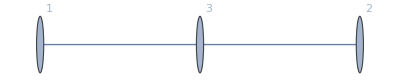

```mathematica
(*The bisegment graph is*)
seseGraph=unlaman[3][[1]]//CanonicalGraph;

(*Note that the following labelling of this "CanonicalGraph" may depend on your version of Mathematica*)
seseGraph//displayGraph
```


-I1[-Graphics-,{l[2],l[3]-pz[1,3]},{z[2,3]}] I2[-Graphics-,{l[1],l[2]+l[3]},{z[1,3]}]+I1[-Graphics-,{l[1],l[3]-pz[2,3]},{z[1,3]}] I2[-Graphics-,{l[1]+l[3],l[2]},{z[2,3]}]

```mathematica
(*Since this is a sliding graph, there is a quadratic relation which can be obtained from it.*)
(*In the quadratic relation, some propagators act "as operators" marked with I1[...], and some are acted upon I2[...]*)
quad[seseGraph]
```

```mathematica
(*Taking the output of a quadratic relation and applying "canonsub" will put the I1 and I2 in canonical order (with the I1s to the left of the I2s) with appropriate signs accounting for edge permutations*)
(*Applying dropsub will then drop the last lambda entry in each of the I1 and I2. i.e. dropping a vertex whose value is implied by momentum conservation*)
quad[seseGraph]/.canonsub/.dropsub
```

-I1[-Graphics-,{l[2]},{z[2,3]}] I2[-Graphics-,{l[1]},{z[1,3]}]+I1[-Graphics-,{l[1]},{z[1,3]}] I2[-Graphics-,{l[1]+l[3]},{-z[2,3]}]

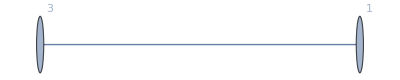
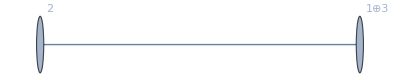
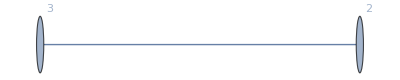
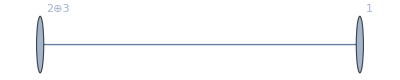
1 | (-Graphics- | {1,3} | {1<->3}
-Graphics- | {1⊕3,2} | {2<->1⊕3})
-1 | (-Graphics- | {2,3} | {2<->3}
-Graphics- | {1,2⊕3} | {1<->2⊕3})

```mathematica
(*We can also see the result in a table as follows:*)
contractGraphSigned[seseGraph]//displayContractionsTable

(*
This result is read as follows:;
	1. In the contraction of the bisegment graph sesegraph 1 <-> 3 <-> 2, we get two terms;
	2. In the first term we contract the 1 <-> 3 edge/subgraph, so 1 <-> 3 becomes an operator acting on the graph 2 <-> (1⊕3);
	3. Then, there is a second term (with overall minus sign) that comes from contracting the 3 <-> 2 edge;

In the language of the table below, the first column is the sign;
The top entry of the second column is the operator graph, while the bottom entry is acted upon;
The third column is the list of vertices that appear in the graphs to the left;
The fourth column is the list of edges that appear in the graphs to the left;
One can check that this produces the same result as quad[sesegraph]/.canonsub/.dropsub;
*)
```

```mathematica
(*There is nothing else of interest to do with this example, as explained in the paper text, as this quadratic relation is trivial*)
```

### Tutorial Example 2: The Triangle Graph (Discrete Symmetries and Shift Symmetries)

```mathematica
(*In the paper, an expression for the triangle graph is computed explicitly, as well as an explicit power series representation.*)
(*Our goal here is just to show how to use some of the functions in this notebook file to understand symmetries of the triangle graph.*)
```

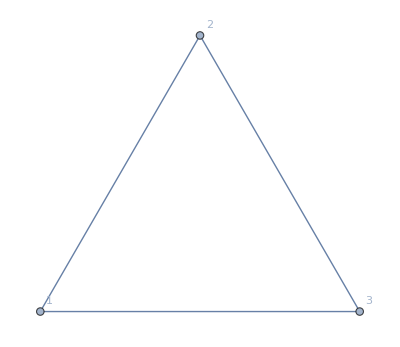

```mathematica
(*The triangle graph looks as follows.*)
triGraph=laman[3][[1]];
triGraph//displayGraph
```

```mathematica
(*We know that the triangle graph has a Subscript[D, 6] ≅ Subscript[S, 3] symmetry group, and that Subscript[S, 3] can be generated by two permutations.*)
(*Two generators of the symmetry group of this graph can be obtained as follows*)
symmetriesOnVerts[triGraph]

(*
WARNING: The result is NOT in cycle notation. The result is read as:;
	1. {1,3,2} means there is a symmetry generator 1->1, 2->3, 3->2;
	2. {2,1,3} means there is a symmetry generator 1->2, 2->1, 3->3;
*)
```

{{1,3,2},{2,1,3}}

```mathematica
(*If one did want to see these manipulations in cycle notation, they can use*)
GraphAutomorphismGroup[triGraph]
```

PermutationGroup[{Cycles[{{2,3}}],Cycles[{{1,2}}]}]

```mathematica
(*Now let's turn to loop variables. We can find a basis of independent cycles automatically, using the function*)
triCycles=triGraph//FindFundamentalCycles

(*Or in the notation of the paper/equations, we identify a good loop variable as*)
(*Note the sign on z[1,3], because it actually appears in the cycle around the loop as 1 <-> 2 <-> 3 <-> 1, but out convention is to write edges z[a,b] with a < b and z[a,b] = - z[b,a]*)
cyclesToLoopVar/@triCycles
```

{{3<->1,1<->2,2<->3}}

{z[1,2]-z[1,3]+z[2,3]}

```mathematica
(*How do the discrete symmetries of the graph manifest on the loop variable? Both give the loop variable an overall minus sign*)
symmetriesOnLoopVars[triGraph]
```

{{ZHold[1]→-ZHold[1]},{ZHold[1]→-ZHold[1]}}

```mathematica
(*Finally, we look at "shift symmetries". The shift symmetries give us the ability to take a function of lambdas and small z's Subscript[I, Γ][λ;z], and write it as;
	Subscript[I, Γ][λ;z] = Exp[g(λ,z)] Subscript[J, Γ][λ;Z]  ;

	i.e. to write it in terms of a function J of ONLY lambdas and LOOP variables (big Z), with an exponential pre-factor whose argument is linear combinations of dot products of λ and small z's: λ.z .;

[[BIG WARNING]] THE CHOICE OF PHASE FUNCTION g[] AND Subscript[J, Γ][] IS NON-UNIQUE! HOWEVER, THIS CODE SHOULD ALWAYS PRODUCE EXPRESSIONS WHICH ARE SELF-CONSISTENT; 
*)
```

```mathematica
(*Mathematica will automatically pick a way to decompose Subscript[I, Γ] using shift symmetries, to see the particular choice, one can use*)
triGraph//VertexList
triGraph//EdgeList
canItoJ[triGraph]
```

{1,2,3}

{1<->2,1<->3,2<->3}

{-z[1,3] λHold[1]-z[2,3] λHold[2],{z[1,2]-z[1,3]+z[2,3]}}

```mathematica
(*To read the output of canItoJ[triGra[h]], it says: given the Mathematica Canonical triangle graph ``triGraph,'' you can decompose:

	Subscript[I, Γ][Subscript[λ, 1],Subscript[λ, 2] ; Subscript[z, 12],Subscript[z, 13],Subscript[z, 23]] = Exp[g(λ_(1,)Subscript[λ, 2] ; Subscript[z, 12],Subscript[z, 13],Subscript[z, 23])] Subscript[J, Γ][Subscript[λ, 1],Subscript[λ, 2] ; Subscript[Z, loop]]  ;
	
	Where one choice is to have the function g(λ,z) = -Subscript[λ, 1]·Subscript[z, 13] - Subscript[λ, 2]·Subscript[z, 23], and loop variable Subscript[Z, loop] = Subscript[z, 12]-Subscript[z, 13]+Subscript[z, 23] ;
*)
```

```mathematica
(*This code will be used extensively throughout to convert quadratic relations involving "I" into much simpler quadratic relations involving only "J", then the desired "I"s can be reconstructed by adding an extra phase.*)
```

### Tutorial Example 3: Triangle Bootstrap (Using the Bootstrap Procedure)

#### Understanding the Quadratic Relation

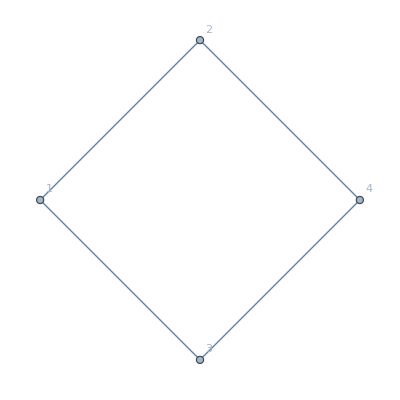

{{4<->2,2<->1,1<->3,3<->4}}

```mathematica
(*The square graph looks as follows.*)
squareGraph=unlaman[4][[1]];
squareGraph//displayGraph
squareGraph//FindFundamentalCycles
```

```mathematica
(*The particular form of the graph (labelling convention) is chosen by Mathematica based on your version, which is why it is always important that the code deal with CanonicalGraphs.*)
(*The final output of the previous block says that there is a loop variable going around the edges of the square.*)
```


-I1[-Graphics-,{l[3]-pz[1,3]},{z[3,4]}] I2[-Graphics-,{l[1],l[2]},{z[1,2],z[1,3],z[2,4]}]+I1[-Graphics-,{l[2]-pz[1,2]},{z[2,4]}] I2[-Graphics-,{l[1],l[2]+l[4]},{z[1,2],z[1,3],-z[3,4]}]+I1[-Graphics-,{l[1]+pz[1,3]},{z[1,2]}] I2[-Graphics-,{l[1]+l[2],l[3]},{z[1,3],z[2,4],z[3,4]}]+I1[-Graphics-,{l[1]+pz[1,2]},{z[1,3]}] I2[-Graphics-,{l[1]+l[3],l[2]},{z[1,2],z[3,4],z[2,4]}]

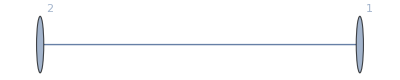
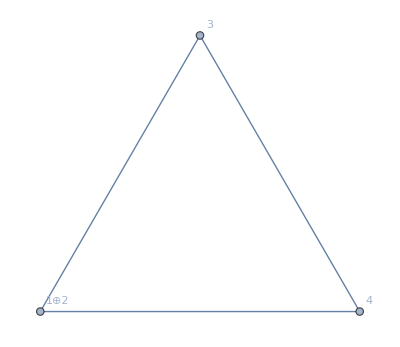
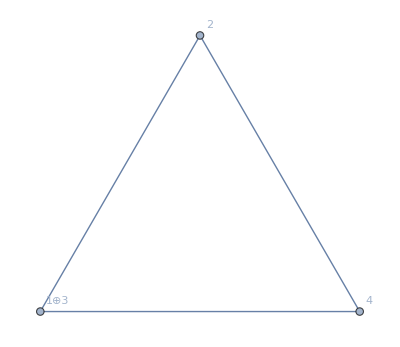
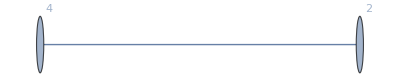
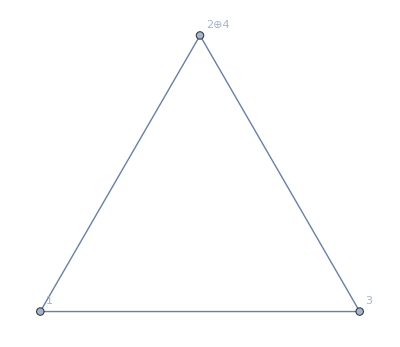
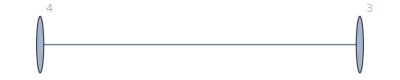
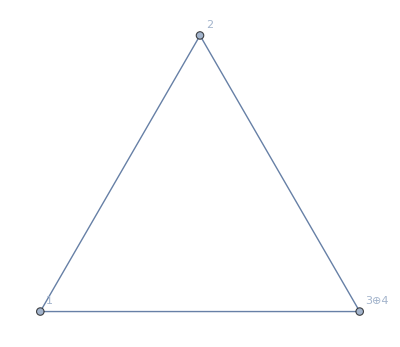
1 | (-Graphics- | {1,2} | {1<->2}
-Graphics- | {1⊕2,3,4} | {1⊕2<->3,1⊕2<->4,3<->4})
1 | (-Graphics- | {1,3} | {1<->3}
-Graphics- | {1⊕3,2,4} | {1⊕3<->2,2<->4,1⊕3<->4})
1 | (-Graphics- | {2,4} | {2<->4}
-Graphics- | {1,2⊕4,3} | {1<->2⊕4,1<->3,3<->2⊕4})
-1 | (-Graphics- | {3,4} | {3<->4}
-Graphics- | {1,2,3⊕4} | {1<->2,1<->3⊕4,2<->3⊕4})

```mathematica
(*The quadratic relation in terms of the variables I is*)
quad[squareGraph]/.canonsub/.dropsub
squareGraph//contractGraphSigned//displayContractionsTable
```

```mathematica
(*To obtain the quadratic relation in terms of the function "J" aka "f" in the paper we simply type:*)
quadJauto[squareGraph]

(*Notice that all of the arguments of the triangle functions only depend on the loop variable coming from the OVERALL unlaman sliding square*)
(*Note that this function also automatically applies all the argument shifts coming from exponentials of derivatives.*)
```

-ⅇ^(-l[2] z[2,4]+l[1] (-z[1,3]-z[3,4])-l[3] z[3,4]) J2[-Graphics-,{l[1],l[2]},{z[1,2]-z[1,3]+z[2,4]-z[3,4]}]+ⅇ^(-l[2] z[2,4]+l[1] (-z[1,3]-z[3,4])-l[3] z[3,4]) J2[-Graphics-,{l[1],-l[1]-l[3]},{z[1,2]-z[1,3]+z[2,4]-z[3,4]}]+ⅇ^(l[1] (-z[1,2]-z[2,4])-l[2] z[2,4]-l[3] z[3,4]) J2[-Graphics-,{l[1]+l[2],l[3]},{-z[1,2]+z[1,3]-z[2,4]+z[3,4]}]+ⅇ^(-l[2] z[2,4]+l[1] (-z[1,3]-z[3,4])-l[3] z[3,4]) J2[-Graphics-,{l[1]+l[3],l[2]},{z[1,2]-z[1,3]+z[2,4]-z[3,4]}]

```mathematica
(*The quadratic relation in terms of just the Js, the loop variable for the square, and with prefactors/expeonentials divided is obtained as follows*)
reducedQuadAuto[squareGraph]

(*
Note that the loop variable ZHold[1] is really "coming from the square graph" as explained in the previous block it is not the loop variable "of the triangle"*)
(*In practice, our future bootstrap calculations will start from the output of this function.
*)
```

-J2[-Graphics-,{l[1],l[2]},{-ZHold[1]}]+J2[-Graphics-,{l[1],-l[1]-l[3]},{-ZHold[1]}]+ⅇ^(l[1] ZHold[1]) J2[-Graphics-,{l[1]+l[2],l[3]},{ZHold[1]}]+J2[-Graphics-,{l[1]+l[3],l[2]},{-ZHold[1]}]

```mathematica
(*FindFundamentalCycles reminds us of what ZHold[1] is*)
squareGraph//FindFundamentalCycles

(*toGoodGlobalLoops tells us how to replace various Subscript[z, ij] quantities in terms of loop quantities*)
squareGraph//toGoodGlobalLoops
```

{{4<->2,2<->1,1<->3,3<->4}}

{pz[1,2]→-pZHold[1],pz[1,3]→pZHold[1],pz[2,4]→-pZHold[1],pz[3,4]→pZHold[1],z[1,3]→z[1,2]+z[2,4]-z[3,4]+ZHold[1]}

#### Implementing the Bootstrap

```mathematica
Clear[Jtri,JtriExact,trico];
(*
To bootstrap the triangle, we need an ansatz for Subscript[f, Triangle] = Subscript[J, Triangle]. This function will take in TWO lambda variables and ONE loop variable Z.;
We know the ansatz should take the form of a charge 0 function, multiplied by a charge 2 object.; 
WLOG this means we can take Subscript[f, Triangle] of the form: (Subscript[λ, 1] ⋀ Subscript[λ, 2]) f[(Subscript[λ, 1]·Z),(Subscript[λ, 2]·Z)] ;
*)
Jtri[{l11_,l12_},{l21_,l22_},{Z11_,Z12_},maxZ_]:=symp[{l11,l12},{l21,l22}]Sum[trico[m,n]mP[l11 Z11+l12 Z12,m]mP[l21 Z11+l22 Z12,n],{m,0,maxZ},{n,0,maxZ}]

(*We include the exact answer.*)
JtriExact[λ1_,λ2_,Z_,maxZ_]:=symp[λ1,λ2]Sum[(-1)^m/Factorial[n+m+2] mP[λ1.Z,m]mP[λ2.Z,n],{n,0,maxZ},{m,0,maxZ}];
```

```mathematica
(*This approach is overpowered, but this is vaguely the efficient way to get things up to order 3 in Z that we will use in the future code*)
maxZ=8;

(*First turn the quadratic relation expression into a separate list of coefficients and expressions. This step isn't actually necessary, we could just do the subs differently... anyway*)
{coefficients,triangles}=List@@reducedQuadAuto[squareGraph]/.{a_. J2[x___]:>{a,J2[x]}}//Transpose

(*Replace the "symbolic dot products" with actual dot products of two component objects, and expand them to order maxZ in the components of the loop variable Z.*)
coefficients=coefficients/.{l[j_]ZHold[i_]:>lm[j].ZL[i]}
coefficients=Series[coefficients,{ZHold[1,1],0,maxZ},{ZHold[1,2],0,maxZ}]//Normal//Expand;

(*Replace the triangles with the Jtri ansatz*)
triangles=(triangles/.{J2[___,{x_,y_},{a_. ZHold[i_]}]:>Jtri[x,y,a ZL[i],maxZ]})/.{l[b_]:>lm[b]};

(*Sew the expressions back together*)
bootstrapMe=coefficients.triangles;

(*We want to only take the expansion "bootstrapMe" up order 8 in Z-loop*)
(*The reason we do it this convoluted way to get the homogeneous degree of Z to be "n" is because doing Z -> eZ then expanding in e will be really time consuming later.*)
arrays=CoefficientArrays[bootstrapMe,ZL[1]];
bootstrapMe=Sum[mDR[arrays[[i]],ZL[1],i-1],{i,1,maxZ+1}];

(*Confirm that we only have coefficients of the ansatz with trico[a,b] such that a+b <= maxZ*)
coefficientList=(bootstrapMe//Expand//Variables)/.{ZHold[___]:>Sequence[],λ[___]:>Sequence[]}

(*This bootstraps the equation, solving for the coefficients in "coefficientList", in polynomials of the variables "lm[1],lm[2],lm[3],lm[4],ZL[1]", by setting bootstrapMe=0*)
ans=seriesToLinEq[bootstrapMe,Flatten[{lm[1],lm[2],lm[3],ZL[1]}],coefficientList]
```

{{-1,1,ⅇ^(l[1] ZHold[1]),1},{J2[-Graphics-,{l[1],l[2]},{-ZHold[1]}],J2[-Graphics-,{l[1],-l[1]-l[3]},{-ZHold[1]}],J2[-Graphics-,{l[1]+l[2],l[3]},{ZHold[1]}],J2[-Graphics-,{l[1]+l[3],l[2]},{-ZHold[1]}]}}

{-1,1,ⅇ^(ZHold[1,1] λ[1,1]+ZHold[1,2] λ[1,2]),1}

{trico[0,0],trico[0,1],trico[1,0],trico[0,2],trico[1,1],trico[0,3],trico[1,2],trico[2,0],trico[2,1],trico[3,0],trico[0,4],trico[1,3],trico[2,2],trico[3,1],trico[0,5],trico[1,4],trico[2,3],trico[3,2],trico[4,0],trico[4,1],trico[5,0],trico[0,6],trico[1,5],trico[2,4],trico[3,3],trico[4,2],trico[5,1],trico[0,7],trico[1,6],trico[2,5],trico[3,4],trico[4,3],trico[5,2],trico[6,0],trico[6,1],trico[7,0],trico[0,8],trico[1,7],trico[2,6],trico[3,5],trico[4,4],trico[5,3],trico[6,2],trico[7,1],trico[8,0]}

{{trico[0,1]→1/3 trico[0,0],trico[0,2]→1/12 trico[0,0],trico[0,3]→1/60 trico[0,0],trico[0,4]→1/360 trico[0,0],trico[0,5]→trico[0,0]/2520,trico[0,6]→trico[0,0]/20160,trico[0,7]→trico[0,0]/181440,trico[0,8]→trico[0,0]/1814400,trico[1,0]→-1/3 trico[0,0],trico[1,1]→-1/12 trico[0,0],trico[1,2]→-1/60 trico[0,0],trico[1,3]→-1/360 trico[0,0],trico[1,4]→-trico[0,0]/2520,trico[1,5]→-trico[0,0]/20160,trico[1,6]→-trico[0,0]/181440,trico[1,7]→-trico[0,0]/1814400,trico[2,0]→1/12 trico[0,0],trico[2,1]→1/60 trico[0,0],trico[2,2]→1/360 trico[0,0],trico[2,3]→trico[0,0]/2520,trico[2,4]→trico[0,0]/20160,trico[2,5]→trico[0,0]/181440,trico[2,6]→trico[0,0]/1814400,trico[3,0]→-1/60 trico[0,0],trico[3,1]→-1/360 trico[0,0],trico[3,2]→-trico[0,0]/2520,trico[3,3]→-trico[0,0]/20160,trico[3,4]→-trico[0,0]/181440,trico[3,5]→-trico[0,0]/1814400,trico[4,0]→1/360 trico[0,0],trico[4,1]→trico[0,0]/2520,trico[4,2]→trico[0,0]/20160,trico[4,3]→trico[0,0]/181440,trico[4,4]→trico[0,0]/1814400,trico[5,0]→-trico[0,0]/2520,trico[5,1]→-trico[0,0]/20160,trico[5,2]→-trico[0,0]/181440,trico[5,3]→-trico[0,0]/1814400,trico[6,0]→trico[0,0]/20160,trico[6,1]→trico[0,0]/181440,trico[6,2]→trico[0,0]/1814400,trico[7,0]→-trico[0,0]/181440,trico[7,1]→-trico[0,0]/1814400,trico[8,0]→trico[0,0]/1814400}}

```mathematica
(*Check answer in a horrifying way*)
ans[[1]]/.{(trico[i_,j_]->a_.trico[0,0]):>{(2(-1)^i)/Factorial[i+j+2]==a}}//Flatten//DeleteDuplicates
```

{True}

### Example: Bitriangle Bootstrap (from the Square-Triangle graph)

#### The Bitriangle Properties

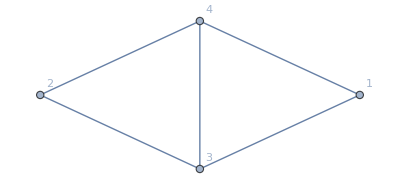

{1<->3,1<->4,2<->3,2<->4,3<->4}

{{4<->1,1<->3,3<->4},{4<->1,1<->3,3<->2,2<->4}}

-z[1,4] λHold[1]+(z[1,3]-z[1,4]-z[2,3]) λHold[2]+(z[1,3]-z[1,4]) λHold[3]

```mathematica
(*The bitriangle graph*)
bitriangle=laman[4][[1]];
bitriangle//displayGraph
bitriangle//EdgeList
bitriangle//FindFundamentalCycles
Collect[canItoJ[bitriangle][[1]],λHold[_]]
```

```mathematica
(*The symmetry group of the bitriangle*)
GraphAutomorphismGroup[bitriangle]
```

PermutationGroup[{Cycles[{{3,4}}],Cycles[{{1,2}}]}]

```mathematica
(*The symmetry group preserves the graphs I, what action do they induce on J/f?*)
decomp=E^(-z[1,4] λ[1]+(z[1,3]-z[1,4]-z[2,3]) λ[2]+(z[1,3]-z[1,4]) λ[3])Jh[{λ[1],λ[2],λ[3]},{z[1,3]-z[1,4]+z[3,4],z[1,3]-z[1,4]-z[2,3]+z[2,4]}];

decomp/(decomp/.{1->2,2->1})/.toGoodGlobalLoops[bitriangle]//Simplify
decomp/(decomp/.{3->4,4->3})/.{λ[4]->-λ[1]-λ[2]-λ[3]}/.toGoodGlobalLoops[bitriangle]//Simplify

(*The above ratio should be this signature at the bottom, reflecting swapping of edges in the graph*)
a11=bitriangle//EdgeList
a21=a11/.{1->2,2->1};
a21=Map[Sort,a21]
Signature[a11]/Signature[a21]

a11=bitriangle//EdgeList
a21=a11/.{3->4,4->3};
a21=Map[Sort,a21]
Signature[a11]/Signature[a21]
```

(ⅇ^(ZHold[2] (λ[1]+λ[2]+λ[3])) Jh[{λ[1],λ[2],λ[3]},{ZHold[1],ZHold[2]}])/Jh[{λ[2],λ[1],λ[3]},{ZHold[1]-ZHold[2],-ZHold[2]}]

(ⅇ^(ZHold[2] λ[2]) Jh[{λ[1],λ[2],λ[3]},{ZHold[1],ZHold[2]}])/Jh[{λ[1],λ[2],-λ[1]-λ[2]-λ[3]},{-ZHold[1],-ZHold[2]}]

{1<->3,1<->4,2<->3,2<->4,3<->4}

{2<->3,2<->4,1<->3,1<->4,3<->4}

1

{1<->3,1<->4,2<->3,2<->4,3<->4}

{1<->4,1<->3,2<->4,2<->3,3<->4}

1

#### The Quadratic Relation

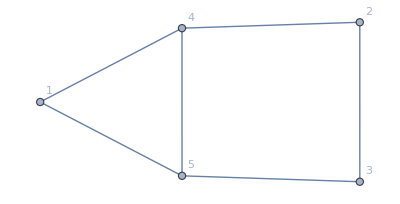

{{5<->1,1<->4,4<->5},{3<->5,5<->1,1<->4,4<->2,2<->3}}

```mathematica
(*The house or square-triangle graph*)
houseGraph=unlaman[5][[3]]//CanonicalGraph;
houseGraph//displayGraph
houseGraph//FindFundamentalCycles
```

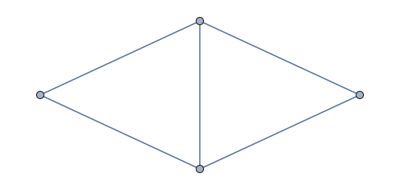
-J1[-Graphics-,{l[1],l[4]+pZHold[2]},{ZHold[1]}] J2[-Graphics-,{-l[2]-l[3],l[2]},{-ZHold[1]+ZHold[2]}]-ⅇ^(l[4] ZHold[1]) J2[-Graphics-,{l[1],l[2],-l[1]-l[2]-l[4]},{-ZHold[1],-ZHold[2]}]-ⅇ^(l[4] ZHold[1]+l[2] ZHold[2]+l[3] ZHold[2]) J2[-Graphics-,{l[1],l[3],l[2]+l[4]},{ZHold[1],ZHold[2]}]+ⅇ^(l[4] ZHold[1]+l[2] ZHold[2]+l[3] ZHold[2]) J2[-Graphics-,{l[1],l[2]+l[3],l[4]},{ZHold[1],ZHold[2]}]

```mathematica
(*The quadratic relation from the square-triangle relation*)
reducedQuadAuto[houseGraph]
```

#### The Bootstrap

```mathematica
(*A taylor series expansion for the bitriangle ansatz up to order maxL in λ*)
BiTriBoot[{l11_,l12_},{l21_,l22_},{l31_,l32_},{Z1_,Z2_},{W1_,W2_},maxL_]:=Sum[If[i+j+k+l+m+n-o-p-q-r==4,d[i,j,k,l,m,n,o,p,q,r]mP[l11,i]mP[l12,j]mP[l21,k]mP[l22,l]mP[l31,m]mP[l32,n]mP[Z1,o]mP[Z2,p]mP[W1,q]mP[W2,r],0],{i,0,maxL},{j,0,maxL-i},{k,0,maxL-i-j},{l,0,maxL-i-j-k},{m,0,maxL-i-j-k-l},{n,0,maxL-i-j-k-l-m},{o,0,maxL-4},{p,0,maxL-4-o},{q,0,maxL-4-o-p},{r,0,maxL-4-o-p-q}]

(*The coefficients that appear in the above series expansion up to order maxL in λ*)
BiTriBootList[maxL_]:=DeleteCases[Table[If[i+j+k+l+m+n-o-p-q-r==4,d[i,j,k,l,m,n,o,p,q,r],-1],{i,0,maxL},{j,0,maxL-i},{k,0,maxL-i-j},{l,0,maxL-i-j-k},{m,0,maxL-i-j-k-l},{n,0,maxL-i-j-k-l-m},{o,0,maxL-4},{p,0,maxL-4-o},{q,0,maxL-4-o-p},{r,0,maxL-4-o-p-q}]//Flatten,-1]
```

```mathematica
(*Break up the quadratic relation into "coefficients", "operators", and "the operated upon"*)
{coeffs,J1s,J2s}=List@@reducedQuadAuto[houseGraph]/.{a_. J1[x___]J2[y___]:>{a,J1[x],J2[y]},a_. J2[y___]:>{a,1,J2[y]}}//Transpose;
coeffs=coeffs/.{Exp[x___]:>Exp[Expand[x]]}/.{l[i_]ZHold[j_]:>lm[i].ZL[j]};

{coeffs,J1s,J2s}//MatrixForm
```

(-1 | -ⅇ^(ZHold[1,1] λ[4,1]+ZHold[1,2] λ[4,2]) | -ⅇ^(ZHold[2,1] λ[2,1]+ZHold[2,2] λ[2,2]+ZHold[2,1] λ[3,1]+ZHold[2,2] λ[3,2]+ZHold[1,1] λ[4,1]+ZHold[1,2] λ[4,2]) | ⅇ^(ZHold[2,1] λ[2,1]+ZHold[2,2] λ[2,2]+ZHold[2,1] λ[3,1]+ZHold[2,2] λ[3,2]+ZHold[1,1] λ[4,1]+ZHold[1,2] λ[4,2])
J1[-Graphics-,{l[1],l[4]+pZHold[2]},{ZHold[1]}] | 1 | 1 | 1
J2[-Graphics-,{-l[2]-l[3],l[2]},{-ZHold[1]+ZHold[2]}] | J2[-Graphics-,{l[1],l[2],-l[1]-l[2]-l[4]},{-ZHold[1],-ZHold[2]}] | J2[-Graphics-,{l[1],l[3],l[2]+l[4]},{ZHold[1],ZHold[2]}] | J2[-Graphics-,{l[1],l[2]+l[3],l[4]},{ZHold[1],ZHold[2]}])

```mathematica
(*The exact answer for the triangle.*)
JtriExact[λ1_,λ2_,Z_,maxZ_]:=symp[λ1,λ2]Sum[(-1)^m/Factorial[n+m+2] mP[λ1.Z,m]mP[λ2.Z,n],{n,0,maxZ},{m,0,maxZ}];
```

```mathematica
maxZ=2;

(*The triangle who is Acting*)
wMM=maxZ;
ActWithMe=JtriExact[lm[1],lm[4],ZL[1],wMM];

(*The Triangle getting Acted on in the quadratic relation you choose*)
oMM=2wMM+2;
ActOnMe=JtriExact[-lm[2]-lm[3],lm[2],-ZL[1]+ZL[2],oMM];

(*
This produces TriTri, aka the (triangle)^2 part;  You have to make sure you load it up with the correct function for your qudratic relations.; 
This says use the function ActWithMe, take it's variable called lm[4], and shift it by lm[4] + (1) * D[#,ZL[2]];
*)
newTriTri=seriesToOperator[ActWithMe,{lm[4]},{{1,ZL[2]}},ActOnMe];
```

```mathematica
(*Since the triangles were SU(2) invariant the triangle acting on the triangle should be SU(2) invariant;
We confirm this is the case for sanity when maxZ=0;
*)
(*
λ[1,1]D[newTriTri,λ[1,2]]+λ[2,1]D[newTriTri,λ[2,2]]+λ[3,1]D[newTriTri,λ[3,2]]+λ[4,1]D[newTriTri,λ[4,2]]-ZHold[1,2]D[newTriTri,ZHold[1,1]]-ZHold[2,2]D[newTriTri,ZHold[2,1]]//Expand
λ[1,2]D[newTriTri,λ[1,1]]+λ[2,2]D[newTriTri,λ[2,1]]+λ[3,2]D[newTriTri,λ[3,1]]+λ[4,2]D[newTriTri,λ[4,1]]-ZHold[1,1]D[newTriTri,ZHold[1,2]]-ZHold[2,1]D[newTriTri,ZHold[2,2]]//Expand
*)
```

```mathematica
(*The list of variables for the polynomials whose coefficients we want to study*)
ZList=Flatten[{ZL[1],ZL[2]}]
varList=Flatten[{Table[lm[i],{i,1,4}],ZList}]

(*An arbitrary bitriangle ansatz*)
bitri=BiTriBoot[lm[1],lm[2],lm[3],ZL[1],ZL[2],4+maxZ];
```

{ZHold[1,1],ZHold[1,2],ZHold[2,1],ZHold[2,2]}

{λ[1,1],λ[1,2],λ[2,1],λ[2,2],λ[3,1],λ[3,2],λ[4,1],λ[4,2],ZHold[1,1],ZHold[1,2],ZHold[2,1],ZHold[2,2]}

```mathematica
(*The code is fastest if we enforce the SU(2) consistency conditions on the arbitrary bitriangle before starting;*)

(*First we have one SU(2) vector field, whose action on bitri should be 0*)
SU21=λ[1,1]D[bitri,λ[1,2]]+λ[2,1]D[bitri,λ[2,2]]+λ[3,1]D[bitri,λ[3,2]]-ZHold[1,2]D[bitri,ZHold[1,1]]-ZHold[2,2]D[bitri,ZHold[2,1]];

(*We use the function seriesToLineq to study the constraints on the unknowns of bitri from this first SU(2) constraint;
The second entry is the "variable list" for the polynomials;
The third entry is the list of coefficients we want to solve for/constrain;
*)
solsSU21=seriesToLinEq[SU21,varList,BiTriBootList[4+maxZ]][[1]];
bitriSU2=bitri/.solsSU21;
bitriSU2//Variables
```

{d[4,0,0,0,0,0,0,0,0,0],λ[1,1],d[4,1,0,0,0,0,0,1,0,0],ZHold[1,1],d[5,0,0,0,0,0,0,1,0,0],ZHold[1,2],d[4,1,0,0,0,0,0,0,0,1],ZHold[2,1],d[5,0,0,0,0,0,0,0,0,1],ZHold[2,2],d[4,2,0,0,0,0,0,2,0,0],d[5,1,0,0,0,0,0,2,0,0],1203,d[0,0,0,0,4,2,0,2,0,0],d[0,0,0,0,5,1,0,2,0,0],d[0,0,0,0,6,0,0,2,0,0],d[0,0,0,0,4,2,0,1,0,1],d[0,0,0,0,6,0,0,1,1,0],d[0,0,0,0,4,2,0,0,0,2],d[0,0,0,0,5,1,0,1,0,1],d[0,0,0,0,6,0,0,1,0,1],d[0,0,0,0,5,1,0,0,0,2],d[0,0,0,0,6,0,0,0,0,2],λ[3,2]}
 |  |  |  |

```mathematica
(*The second SU(2) constraint can be enforce similarly*)
SU22=λ[1,2]D[bitriSU2,λ[1,1]]+λ[2,2]D[bitriSU2,λ[2,1]]+λ[3,2]D[bitriSU2,λ[3,1]]-ZHold[1,1]D[bitriSU2,ZHold[1,2]]-ZHold[2,1]D[bitriSU2,ZHold[2,2]];
solsSU22=seriesToLinEq[SU22,varList,BiTriBootList[4+maxZ]][[1]];
bitriSU22=bitriSU2/.solsSU22;
bitriSU22//Variables
```

{d[0,2,2,0,0,0,0,0,0,0],λ[1,2],λ[2,1],d[0,3,2,0,0,0,0,1,0,0],ZHold[1,1],λ[1,1],d[0,3,2,0,0,0,0,0,0,1],ZHold[2,1],d[0,4,2,0,0,0,0,2,0,0],d[0,4,2,0,0,0,0,1,0,1],d[0,4,2,0,0,0,0,0,0,2],ZHold[1,2],ZHold[2,2],d[0,2,2,1,0,0,0,1,0,0],d[0,2,2,1,0,0,0,0,0,1],d[0,3,2,1,0,0,0,2,0,0],d[0,3,2,1,0,0,0,1,0,1],d[0,3,2,1,0,0,0,0,0,2],d[0,3,3,0,0,0,0,1,1,0],d[0,2,2,2,0,0,0,2,0,0],d[0,2,2,2,0,0,0,1,0,1],d[0,2,2,2,0,0,0,0,0,2],λ[2,2],d[0,2,1,0,1,0,0,0,0,0],λ[3,1],d[0,3,1,0,1,0,0,1,0,0],d[0,3,1,0,1,0,0,0,0,1],d[0,4,1,0,1,0,0,2,0,0],d[0,4,1,0,1,0,0,1,0,1],d[0,4,1,0,1,0,0,0,0,2],d[0,2,1,1,1,0,0,1,0,0],d[0,2,2,0,0,1,0,1,0,0],d[0,2,1,1,1,0,0,0,0,1],d[0,2,2,0,0,1,0,0,0,1],d[0,3,1,1,1,0,0,2,0,0],d[0,3,2,0,0,1,0,2,0,0],d[0,3,1,1,1,0,0,1,0,1],d[0,3,2,0,0,1,0,1,0,1],d[0,3,1,1,1,0,0,0,0,2],d[0,3,2,0,0,1,0,0,0,2],d[0,3,2,0,1,0,0,1,1,0],d[0,2,1,2,1,0,0,2,0,0],d[0,2,2,1,0,1,0,2,0,0],d[0,2,1,2,1,0,0,1,0,1],d[0,2,2,1,0,1,0,1,0,1],d[0,2,1,2,1,0,0,0,0,2],d[0,2,2,1,0,1,0,0,0,2],d[0,1,1,1,1,0,0,0,0,0],d[0,1,1,2,1,0,0,1,0,0],d[0,1,1,2,1,0,0,0,0,1],d[0,2,2,1,1,0,0,1,1,0],d[0,1,1,3,1,0,0,2,0,0],d[0,1,1,3,1,0,0,1,0,1],d[0,1,1,3,1,0,0,0,0,2],d[0,2,0,0,2,0,0,0,0,0],d[0,3,0,0,2,0,0,1,0,0],d[0,3,0,0,2,0,0,0,0,1],d[0,4,0,0,2,0,0,2,0,0],d[0,4,0,0,2,0,0,1,0,1],d[0,4,0,0,2,0,0,0,0,2],d[0,2,0,1,2,0,0,1,0,0],d[0,2,1,0,1,1,0,1,0,0],d[0,2,0,1,2,0,0,0,0,1],d[0,2,1,0,1,1,0,0,0,1],d[0,3,0,1,2,0,0,2,0,0],d[0,3,1,0,1,1,0,2,0,0],d[0,3,0,1,2,0,0,1,0,1],d[0,3,1,0,1,1,0,1,0,1],d[0,3,0,1,2,0,0,0,0,2],d[0,3,1,0,1,1,0,0,0,2],d[0,3,1,0,2,0,0,1,1,0],d[0,2,0,2,2,0,0,2,0,0],d[0,2,1,1,1,1,0,2,0,0],d[0,2,2,0,0,2,0,2,0,0],d[0,2,0,2,2,0,0,1,0,1],d[0,2,1,1,1,1,0,1,0,1],d[0,2,2,0,0,2,0,1,0,1],d[0,2,0,2,2,0,0,0,0,2],d[0,2,1,1,1,1,0,0,0,2],d[0,2,2,0,0,2,0,0,0,2],d[0,1,0,1,2,0,0,0,0,0],d[0,1,0,2,2,0,0,1,0,0],d[0,1,1,1,1,1,0,1,0,0],d[0,1,0,2,2,0,0,0,0,1],d[0,1,1,1,1,1,0,0,0,1],d[0,2,1,1,2,0,0,1,1,0],d[0,1,0,3,2,0,0,2,0,0],d[0,1,1,2,1,1,0,2,0,0],d[0,1,0,3,2,0,0,1,0,1],d[0,1,1,2,1,1,0,1,0,1],d[0,1,0,3,2,0,0,0,0,2],d[0,1,1,2,1,1,0,0,0,2],d[0,0,0,2,2,0,0,0,0,0],d[0,0,0,3,2,0,0,1,0,0],d[0,0,0,3,2,0,0,0,0,1],d[0,1,1,2,2,0,0,1,1,0],d[0,0,0,4,2,0,0,2,0,0],d[0,0,0,4,2,0,0,1,0,1],d[0,0,0,4,2,0,0,0,0,2],d[0,2,0,0,2,1,0,1,0,0],d[0,2,0,0,2,1,0,0,0,1],d[0,3,0,0,2,1,0,2,0,0],d[0,3,0,0,2,1,0,1,0,1],d[0,3,0,0,2,1,0,0,0,2],d[0,3,0,0,3,0,0,1,1,0],d[0,2,0,1,2,1,0,2,0,0],d[0,2,1,0,1,2,0,2,0,0],d[0,2,0,1,2,1,0,1,0,1],d[0,2,1,0,1,2,0,1,0,1],d[0,2,0,1,2,1,0,0,0,2],d[0,2,1,0,1,2,0,0,0,2],d[0,1,0,1,2,1,0,1,0,0],d[0,1,0,1,2,1,0,0,0,1],d[0,2,0,1,3,0,0,1,1,0],d[0,1,0,2,2,1,0,2,0,0],d[0,1,1,1,1,2,0,2,0,0],d[0,1,0,2,2,1,0,1,0,1],d[0,1,1,1,1,2,0,1,0,1],d[0,1,0,2,2,1,0,0,0,2],d[0,1,1,1,1,2,0,0,0,2],d[0,0,0,2,2,1,0,1,0,0],d[0,0,0,2,2,1,0,0,0,1],d[0,1,0,2,3,0,0,1,1,0],d[0,0,0,3,2,1,0,2,0,0],d[0,0,0,3,2,1,0,1,0,1],d[0,0,0,3,2,1,0,0,0,2],d[0,0,0,3,3,0,0,1,1,0],d[0,2,0,0,2,2,0,2,0,0],d[0,2,0,0,2,2,0,1,0,1],d[0,2,0,0,2,2,0,0,0,2],d[0,1,0,1,2,2,0,2,0,0],d[0,1,0,1,2,2,0,1,0,1],d[0,1,0,1,2,2,0,0,0,2],d[0,0,0,2,2,2,0,2,0,0],d[0,0,0,2,2,2,0,1,0,1],d[0,0,0,2,2,2,0,0,0,2],λ[3,2]}

```mathematica
(*The bitriangle ansatz with the SU(2) constraints imposed*)
BiTriBootSU2[l1_,l2_,l3_,Z1_,Z2_,len_]:=BiTriBoot[l1,l2,l3,Z1,Z2,len]/.solsSU21/.solsSU22
```

```mathematica
(*The bitriangles are replaced with the new SU(2) invariant bitriangle*)
bitris=((J2s[[2;;4]]/.{l[i_]:>lm[i],ZHold[j_]:>ZL[j]})/.{J2[bitri_,{l1__,l2__,l3__},{Z1__,Z2__}]:>BiTriBootSU2[l1,l2,l3,Z1,Z2,4+maxZ]});
```

```mathematica
(*We reassemble the operators; 
Note that we have to put an extra coefficient infront of newTriTri  because the function seriesToLinEq throws away everything that doesn't have exactly weight 1 in the coefficients we're solving for;
*)
nocoeffs={tritriCo newTriTri,bitris}//Flatten;
(*Add the coefficients back in and expand the exponentials*)
bootstrapMe=nocoeffs.(coeffs/.{Exp[x_]:>Sum[x^ik/Factorial[ik],{ik,0,maxZ}]});
(*Only take things up to and including things with order maxZ=2 in Z variables*)
arrays=CoefficientArrays[bootstrapMe,ZList];
bootstrapMe=Sum[mDR[arrays[[i]],ZList,i-1],{i,1,maxZ+1}];
```

```mathematica
(*We solve the quadratic relations*)
sols=seriesToLinEq[bootstrapMe,varList,Flatten[{BiTriBootList[4+maxZ],tritriCo}]][[1]];
ans=BiTriBootSU2[lm[1],lm[2],lm[3],ZL[1],ZL[2],4+maxZ]/.sols//Expand;

(*some unknowns still remain, even after using the quadratic relation! But we still need to use symmetries.*)
(ans//Variables)/.{λ[___]:>Sequence[],ZHold[___]:>Sequence[]}
```

{tritriCo,d[0,3,1,0,1,0,0,1,0,0],d[0,3,1,0,1,0,0,0,0,1],d[0,3,0,1,2,0,0,2,0,0],d[0,3,0,1,2,0,0,1,0,1],d[0,3,0,1,2,0,0,0,0,2],d[0,3,1,0,2,0,0,1,1,0]}

```mathematica
(*Before proceeding, let's double check that our bitriangle equation (with SU(2) invariance and quadratic relations imposed) actually satisfies the quadratic identity and SU(2) invariant equations (i.e. make sure nothing has been done incorrectly)*)
bootstrapMe/.sols//Expand
λ[1,1]D[ans,λ[1,2]]+λ[2,1]D[ans,λ[2,2]]+λ[3,1]D[ans,λ[3,2]]-ZHold[1,2]D[ans,ZHold[1,1]]-ZHold[2,2]D[ans,ZHold[2,1]]//Expand
λ[1,2]D[ans,λ[1,1]]+λ[2,2]D[ans,λ[2,1]]+λ[3,2]D[ans,λ[3,1]]-ZHold[1,1]D[ans,ZHold[1,2]]-ZHold[2,1]D[ans,ZHold[2,2]]//Expand
```

0

0

0

```mathematica
(*Imposing JUST the 12 symmetry generator constraint*)
ans12Swapped=ans/.{λ[2,i_]:>λ[1,i],λ[1,j_]:>λ[2,j],ZHold[1,k_]:>ZHold[1,k]-ZHold[2,k],ZHold[2,l_]:>-ZHold[2,l]};
ans12Swapped=(Exp[-(lm[1]+lm[2]+lm[3]).(ZL[2])]/.{Exp[x_]:>Sum[x^ik/Factorial[ik],{ik,0,maxZ}]})*ans12Swapped;
arr12=CoefficientArrays[ans12Swapped,ZList];
ans12Swapped=Sum[mDR[arr12[[i]],ZList,i-1],{i,1,maxZ+1}];

(*We find we fix all the remaining coefficients!*)
sym12SwappedSols=seriesToLinEq[ans-ans12Swapped,varList,Flatten[{BiTriBootList[4+maxZ],tritriCo}]][[1]]
```

{d[0,3,0,1,2,0,0,0,0,2]→tritriCo/360,d[0,3,0,1,2,0,0,1,0,1]→tritriCo/180,d[0,3,0,1,2,0,0,2,0,0]→tritriCo/120,d[0,3,1,0,1,0,0,0,0,1]→tritriCo/72,d[0,3,1,0,1,0,0,1,0,0]→tritriCo/36,d[0,3,1,0,2,0,0,1,1,0]→-tritriCo/180}

```mathematica
(*The final bitriangle answer is (with overall normalization/scaling coefficient).*)
bitriangleAns=ans/.sym12SwappedSols
```

-1/24 tritriCo λ[1,2]^2 λ[2,1]^2+1/72 tritriCo ZHold[1,1] λ[1,1] λ[1,2]^2 λ[2,1]^2+1/144 tritriCo ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1]^2-1/320 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[1,2]^2 λ[2,1]^2-1/480 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[1,2]^2 λ[2,1]^2-1/960 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[1,2]^2 λ[2,1]^2+1/72 tritriCo ZHold[1,2] λ[1,2]^3 λ[2,1]^2+1121+1/40 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,1] λ[3,2]^4+1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,1] λ[3,2]^4+1/120 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,1] λ[3,2]^4
 |  |  |  |

```mathematica
decomp/(decomp/.{3->4,4->3})/.{λ[4]->-λ[1]-λ[2]-λ[3]}/.toGoodGlobalLoops[bitriangle]//Simplify
```

(ⅇ^(ZHold[2] λ[2]) Jh[{λ[1],λ[2],λ[3]},{ZHold[1],ZHold[2]}])/Jh[{λ[1],λ[2],-λ[1]-λ[2]-λ[3]},{-ZHold[1],-ZHold[2]}]

```mathematica
(*We should confirm that the other Z2 symmetry is respected*)
ans34Swapped=bitriangleAns/.{λ[3,i_]:>-λ[1,i]-λ[2,i]-λ[3,i],ZHold[1,k_]:>-ZHold[1,k],ZHold[2,l_]:>-ZHold[2,l]};
ans34Swapped=(Exp[-lm[2].ZL[2]]/.{Exp[x_]:>Sum[x^ik/Factorial[ik],{ik,0,maxZ}]})*ans34Swapped;
arr34=CoefficientArrays[ans34Swapped,ZList];
ans34Swapped=Sum[mDR[arr34[[i]],ZList,i-1],{i,1,maxZ+1}];

ans34Swapped-bitriangleAns//Expand
```

0

#### 2 Loop J_{bitriangle}. You can run this if you do not want to run the above bootstrap again. Variable is called “bitriangleAns”

```mathematica
bitriangleAns=-1/24 tritriCo λ[1,2]^2 λ[2,1]^2+1/72 tritriCo ZHold[1,1] λ[1,1] λ[1,2]^2 λ[2,1]^2+1/144 tritriCo ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1]^2-1/320 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[1,2]^2 λ[2,1]^2-1/480 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[1,2]^2 λ[2,1]^2-1/960 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[1,2]^2 λ[2,1]^2+1/72 tritriCo ZHold[1,2] λ[1,2]^3 λ[2,1]^2+1/144 tritriCo ZHold[2,2] λ[1,2]^3 λ[2,1]^2-1/160 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2]^3 λ[2,1]^2-1/480 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2]^3 λ[2,1]^2-1/480 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2]^3 λ[2,1]^2-1/480 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2]^3 λ[2,1]^2-1/320 tritriCo ZHold[1,2]^2 λ[1,2]^4 λ[2,1]^2-1/480 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^4 λ[2,1]^2-1/960 tritriCo ZHold[2,2]^2 λ[1,2]^4 λ[2,1]^2+1/72 tritriCo ZHold[1,1] λ[1,2]^2 λ[2,1]^3+1/48 tritriCo ZHold[2,1] λ[1,2]^2 λ[2,1]^3-1/180 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2]^2 λ[2,1]^3-1/120 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1]^3-1/240 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2]^2 λ[2,1]^3-1/180 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^3 λ[2,1]^3-(7 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^3 λ[2,1]^3)/1080-1/540 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^3 λ[2,1]^3-1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^3 λ[2,1]^3-1/320 tritriCo ZHold[1,1]^2 λ[1,2]^2 λ[2,1]^4-1/180 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2]^2 λ[2,1]^4-1/160 tritriCo ZHold[2,1]^2 λ[1,2]^2 λ[2,1]^4+1/12 tritriCo λ[1,1] λ[1,2] λ[2,1] λ[2,2]-1/36 tritriCo ZHold[1,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2]-1/72 tritriCo ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2]+1/160 tritriCo ZHold[1,1]^2 λ[1,1]^3 λ[1,2] λ[2,1] λ[2,2]+1/240 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^3 λ[1,2] λ[2,1] λ[2,2]+1/480 tritriCo ZHold[2,1]^2 λ[1,1]^3 λ[1,2] λ[2,1] λ[2,2]-1/36 tritriCo ZHold[1,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2]-1/72 tritriCo ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2]+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[2,2]+1/240 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[2,2]+1/240 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[2,2]+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[2,2]+1/160 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2]^3 λ[2,1] λ[2,2]+1/240 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2]^3 λ[2,1] λ[2,2]+1/480 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2]^3 λ[2,1] λ[2,2]-1/36 tritriCo ZHold[1,1] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2]-1/24 tritriCo ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2]+1/90 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[1,2] λ[2,1]^2 λ[2,2]+1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1]^2 λ[2,2]+1/120 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[1,2] λ[2,1]^2 λ[2,2]+1/72 tritriCo ZHold[1,2] λ[1,2]^2 λ[2,1]^2 λ[2,2]+1/48 tritriCo ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[2,2]+1/180 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[2,2]+1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[2,2]-1/360 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[2,2]+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[2,2]-1/180 tritriCo ZHold[1,2]^2 λ[1,2]^3 λ[2,1]^2 λ[2,2]-1/120 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^3 λ[2,1]^2 λ[2,2]-1/240 tritriCo ZHold[2,2]^2 λ[1,2]^3 λ[2,1]^2 λ[2,2]+1/160 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2] λ[2,1]^3 λ[2,2]+1/90 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^3 λ[2,2]+1/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2] λ[2,1]^3 λ[2,2]-1/160 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^2 λ[2,1]^3 λ[2,2]-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^2 λ[2,1]^3 λ[2,2]-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^2 λ[2,1]^3 λ[2,2]-1/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^2 λ[2,1]^3 λ[2,2]-1/24 tritriCo λ[1,1]^2 λ[2,2]^2+1/72 tritriCo ZHold[1,1] λ[1,1]^3 λ[2,2]^2+1/144 tritriCo ZHold[2,1] λ[1,1]^3 λ[2,2]^2-1/320 tritriCo ZHold[1,1]^2 λ[1,1]^4 λ[2,2]^2-1/480 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^4 λ[2,2]^2-1/960 tritriCo ZHold[2,1]^2 λ[1,1]^4 λ[2,2]^2+1/72 tritriCo ZHold[1,2] λ[1,1]^2 λ[1,2] λ[2,2]^2+1/144 tritriCo ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2]^2-1/160 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^3 λ[1,2] λ[2,2]^2-1/480 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^3 λ[1,2] λ[2,2]^2-1/480 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^3 λ[1,2] λ[2,2]^2-1/480 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^3 λ[1,2] λ[2,2]^2-1/320 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[1,2]^2 λ[2,2]^2-1/480 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[1,2]^2 λ[2,2]^2-1/960 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[1,2]^2 λ[2,2]^2+1/72 tritriCo ZHold[1,1] λ[1,1]^2 λ[2,1] λ[2,2]^2+1/48 tritriCo ZHold[2,1] λ[1,1]^2 λ[2,1] λ[2,2]^2-1/180 tritriCo ZHold[1,1]^2 λ[1,1]^3 λ[2,1] λ[2,2]^2-1/120 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^3 λ[2,1] λ[2,2]^2-1/240 tritriCo ZHold[2,1]^2 λ[1,1]^3 λ[2,1] λ[2,2]^2-1/36 tritriCo ZHold[1,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2-1/24 tritriCo ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2+1/180 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2]^2-1/360 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2]^2+1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2]^2+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2]^2+1/90 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2]^2+1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2]^2+1/120 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2]^2-1/320 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[2,1]^2 λ[2,2]^2-1/180 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[2,1]^2 λ[2,2]^2-1/160 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[2,1]^2 λ[2,2]^2+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2]^2+1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2]^2+1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2]^2+1/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2]^2-1/320 tritriCo ZHold[1,2]^2 λ[1,2]^2 λ[2,1]^2 λ[2,2]^2-1/180 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[2,2]^2-1/160 tritriCo ZHold[2,2]^2 λ[1,2]^2 λ[2,1]^2 λ[2,2]^2+1/72 tritriCo ZHold[1,2] λ[1,1]^2 λ[2,2]^3+1/48 tritriCo ZHold[2,2] λ[1,1]^2 λ[2,2]^3-1/180 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^3 λ[2,2]^3-1/540 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^3 λ[2,2]^3-(7 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^3 λ[2,2]^3)/1080-1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^3 λ[2,2]^3-1/180 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[1,2] λ[2,2]^3-1/120 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2]^3-1/240 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[1,2] λ[2,2]^3-1/160 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[2,1] λ[2,2]^3-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[2,1] λ[2,2]^3-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[2,1] λ[2,2]^3-1/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[2,1] λ[2,2]^3+1/160 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2] λ[2,1] λ[2,2]^3+1/90 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2]^3+1/80 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2] λ[2,1] λ[2,2]^3-1/320 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[2,2]^4-1/180 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[2,2]^4-1/160 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[2,2]^4-1/12 tritriCo λ[1,2]^2 λ[2,1] λ[3,1]+1/36 tritriCo ZHold[1,1] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1]+1/72 tritriCo ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1]-1/160 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[3,1]-1/240 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[3,1]-1/480 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[3,1]+1/36 tritriCo ZHold[1,2] λ[1,2]^3 λ[2,1] λ[3,1]+1/72 tritriCo ZHold[2,2] λ[1,2]^3 λ[2,1] λ[3,1]-1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2]^3 λ[2,1] λ[3,1]-1/240 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2]^3 λ[2,1] λ[3,1]-1/240 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2]^3 λ[2,1] λ[3,1]-1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2]^3 λ[2,1] λ[3,1]-1/160 tritriCo ZHold[1,2]^2 λ[1,2]^4 λ[2,1] λ[3,1]-1/240 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^4 λ[2,1] λ[3,1]-1/480 tritriCo ZHold[2,2]^2 λ[1,2]^4 λ[2,1] λ[3,1]+1/24 tritriCo ZHold[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,1]+1/16 tritriCo ZHold[2,1] λ[1,2]^2 λ[2,1]^2 λ[3,1]-1/60 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,1]-1/40 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,1]-1/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,1]-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^3 λ[2,1]^2 λ[3,1]-7/360 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^3 λ[2,1]^2 λ[3,1]-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^3 λ[2,1]^2 λ[3,1]-1/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^3 λ[2,1]^2 λ[3,1]-1/80 tritriCo ZHold[1,1]^2 λ[1,2]^2 λ[2,1]^3 λ[3,1]-1/45 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2]^2 λ[2,1]^3 λ[3,1]-1/40 tritriCo ZHold[2,1]^2 λ[1,2]^2 λ[2,1]^3 λ[3,1]+1/12 tritriCo λ[1,1] λ[1,2] λ[2,2] λ[3,1]-1/36 tritriCo ZHold[1,1] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1]-1/72 tritriCo ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1]+1/160 tritriCo ZHold[1,1]^2 λ[1,1]^3 λ[1,2] λ[2,2] λ[3,1]+1/240 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^3 λ[1,2] λ[2,2] λ[3,1]+1/480 tritriCo ZHold[2,1]^2 λ[1,1]^3 λ[1,2] λ[2,2] λ[3,1]-1/36 tritriCo ZHold[1,2] λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1]-1/72 tritriCo ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1]+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[1,2]^2 λ[2,2] λ[3,1]+1/240 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[1,2]^2 λ[2,2] λ[3,1]+1/240 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[1,2]^2 λ[2,2] λ[3,1]+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[1,2]^2 λ[2,2] λ[3,1]+1/160 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2]^3 λ[2,2] λ[3,1]+1/240 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2]^3 λ[2,2] λ[3,1]+1/480 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2]^3 λ[2,2] λ[3,1]+1/12 tritriCo λ[1,2] λ[2,1] λ[2,2] λ[3,1]-1/12 tritriCo ZHold[1,1] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]-1/12 tritriCo ZHold[2,1] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]+7/240 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,1]+1/30 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,1]+1/60 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,1]+1/24 tritriCo ZHold[2,2] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]+1/45 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]+1/120 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]-1/240 tritriCo ZHold[1,2]^2 λ[1,2]^3 λ[2,1] λ[2,2] λ[3,1]-1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^3 λ[2,1] λ[2,2] λ[3,1]-1/120 tritriCo ZHold[2,2]^2 λ[1,2]^3 λ[2,1] λ[2,2] λ[3,1]-1/36 tritriCo ZHold[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1]-1/24 tritriCo ZHold[2,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1]+7/240 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1]+17/360 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1]+3/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1]-1/120 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,1]-1/360 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,1]-1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,1]-3/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,1]+1/160 tritriCo ZHold[1,1]^2 λ[1,2] λ[2,1]^3 λ[2,2] λ[3,1]+1/90 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2] λ[2,1]^3 λ[2,2] λ[3,1]+1/80 tritriCo ZHold[2,1]^2 λ[1,2] λ[2,1]^3 λ[2,2] λ[3,1]-1/12 tritriCo λ[1,1] λ[2,2]^2 λ[3,1]+1/24 tritriCo ZHold[1,1] λ[1,1]^2 λ[2,2]^2 λ[3,1]+1/48 tritriCo ZHold[2,1] λ[1,1]^2 λ[2,2]^2 λ[3,1]-1/80 tritriCo ZHold[1,1]^2 λ[1,1]^3 λ[2,2]^2 λ[3,1]-1/120 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^3 λ[2,2]^2 λ[3,1]-1/240 tritriCo ZHold[2,1]^2 λ[1,1]^3 λ[2,2]^2 λ[3,1]-1/24 tritriCo ZHold[2,2] λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1]-1/120 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,1]-1/360 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,1]+1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,1]+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,1]+1/240 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2]^2 λ[2,2]^2 λ[3,1]+1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,2]^2 λ[3,1]+1/120 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2]^2 λ[2,2]^2 λ[3,1]+1/36 tritriCo ZHold[1,1] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1]+1/24 tritriCo ZHold[2,1] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1]-1/60 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,1]-1/40 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,1]-1/80 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,1]-1/36 tritriCo ZHold[1,2] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]-1/24 tritriCo ZHold[2,2] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]+1/120 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]+13/360 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]+1/20 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]+1/240 tritriCo ZHold[1,2]^2 λ[1,2]^2 λ[2,1] λ[2,2]^2 λ[3,1]+1/360 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^2 λ[2,1] λ[2,2]^2 λ[3,1]-1/80 tritriCo ZHold[2,2]^2 λ[1,2]^2 λ[2,1] λ[2,2]^2 λ[3,1]-1/160 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,1]^2 λ[2,2]^2 λ[3,1]-1/90 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,1]^2 λ[2,2]^2 λ[3,1]-1/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,1]^2 λ[2,2]^2 λ[3,1]+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,1]^2 λ[2,2]^2 λ[3,1]+1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,1]^2 λ[2,2]^2 λ[3,1]+1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[2,2]^2 λ[3,1]+1/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[2,2]^2 λ[3,1]+1/36 tritriCo ZHold[1,2] λ[1,1] λ[2,2]^3 λ[3,1]+1/24 tritriCo ZHold[2,2] λ[1,1] λ[2,2]^3 λ[3,1]-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[2,2]^3 λ[3,1]-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[2,2]^3 λ[3,1]-7/360 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[2,2]^3 λ[3,1]-1/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[2,2]^3 λ[3,1]-1/240 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2] λ[2,2]^3 λ[3,1]-1/360 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2] λ[2,2]^3 λ[3,1]+1/80 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2] λ[2,2]^3 λ[3,1]-1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,1] λ[2,2]^3 λ[3,1]-1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,1] λ[2,2]^3 λ[3,1]-1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2]^3 λ[3,1]-1/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2]^3 λ[3,1]+1/160 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,1] λ[2,2]^3 λ[3,1]+1/90 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,1] λ[2,2]^3 λ[3,1]+1/80 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,1] λ[2,2]^3 λ[3,1]-1/160 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,2]^4 λ[3,1]-1/90 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,2]^4 λ[3,1]-1/80 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,2]^4 λ[3,1]+1/24 tritriCo ZHold[1,1] λ[1,2]^2 λ[2,1] λ[3,1]^2+1/48 tritriCo ZHold[2,1] λ[1,2]^2 λ[2,1] λ[3,1]^2-1/60 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1]^2-1/90 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1]^2-1/180 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1]^2-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^3 λ[2,1] λ[3,1]^2-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^3 λ[2,1] λ[3,1]^2-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^3 λ[2,1] λ[3,1]^2-1/180 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^3 λ[2,1] λ[3,1]^2-3/160 tritriCo ZHold[1,1]^2 λ[1,2]^2 λ[2,1]^2 λ[3,1]^2-1/30 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2]^2 λ[2,1]^2 λ[3,1]^2-1/60 tritriCo ZHold[2,1]^2 λ[1,2]^2 λ[2,1]^2 λ[3,1]^2+1/6 tritriCo λ[1,2] λ[2,2] λ[3,1]^2-1/12 tritriCo ZHold[1,1] λ[1,1] λ[1,2] λ[2,2] λ[3,1]^2-1/24 tritriCo ZHold[2,1] λ[1,1] λ[1,2] λ[2,2] λ[3,1]^2+1/40 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1]^2+1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1]^2+1/120 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1]^2-1/24 tritriCo ZHold[1,2] λ[1,2]^2 λ[2,2] λ[3,1]^2-1/48 tritriCo ZHold[2,2] λ[1,2]^2 λ[2,2] λ[3,1]^2+1/30 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1]^2+1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1]^2+1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1]^2+1/90 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1]^2+1/120 tritriCo ZHold[1,2]^2 λ[1,2]^3 λ[2,2] λ[3,1]^2+1/180 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^3 λ[2,2] λ[3,1]^2+1/360 tritriCo ZHold[2,2]^2 λ[1,2]^3 λ[2,2] λ[3,1]^2-1/12 tritriCo ZHold[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2-1/8 tritriCo ZHold[2,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2+1/20 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2+3/40 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2+3/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]^2+1/40 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]^2-1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]^2+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]^2+1/40 tritriCo ZHold[1,1]^2 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1]^2+2/45 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1]^2+1/20 tritriCo ZHold[2,1]^2 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1]^2+1/24 tritriCo ZHold[1,1] λ[1,1] λ[2,2]^2 λ[3,1]^2+1/48 tritriCo ZHold[2,1] λ[1,1] λ[2,2]^2 λ[3,1]^2-3/160 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[2,2]^2 λ[3,1]^2-1/80 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[2,2]^2 λ[3,1]^2-1/160 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[2,2]^2 λ[3,1]^2-1/24 tritriCo ZHold[1,2] λ[1,2] λ[2,2]^2 λ[3,1]^2-5/48 tritriCo ZHold[2,2] λ[1,2] λ[2,2]^2 λ[3,1]^2+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1]^2+1/240 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1]^2+11/240 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1]^2+1/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1]^2+1/80 tritriCo ZHold[1,2]^2 λ[1,2]^2 λ[2,2]^2 λ[3,1]^2+7/240 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^2 λ[2,2]^2 λ[3,1]^2+7/480 tritriCo ZHold[2,2]^2 λ[1,2]^2 λ[2,2]^2 λ[3,1]^2-1/60 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1]^2-1/40 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1]^2-1/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1]^2+1/30 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]^2+1/40 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]^2+7/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]^2+7/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]^2-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,2]^3 λ[3,1]^2-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,2]^3 λ[3,1]^2-7/360 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,2]^3 λ[3,1]^2-1/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,2]^3 λ[3,1]^2+1/120 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,2]^3 λ[3,1]^2+7/360 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,2]^3 λ[3,1]^2+3/80 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,2]^3 λ[3,1]^2-1/80 tritriCo ZHold[1,1]^2 λ[1,2]^2 λ[2,1] λ[3,1]^3-1/120 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2]^2 λ[2,1] λ[3,1]^3-1/240 tritriCo ZHold[2,1]^2 λ[1,2]^2 λ[2,1] λ[3,1]^3-1/12 tritriCo ZHold[1,1] λ[1,2] λ[2,2] λ[3,1]^3-1/24 tritriCo ZHold[2,1] λ[1,2] λ[2,2] λ[3,1]^3+3/80 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2] λ[2,2] λ[3,1]^3+1/40 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2] λ[2,2] λ[3,1]^3+1/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2] λ[2,2] λ[3,1]^3+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^2 λ[2,2] λ[3,1]^3+1/120 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^2 λ[2,2] λ[3,1]^3+1/120 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^2 λ[2,2] λ[3,1]^3+1/120 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^2 λ[2,2] λ[3,1]^3+3/80 tritriCo ZHold[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,1]^3+1/15 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^3+1/30 tritriCo ZHold[2,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,1]^3-1/80 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,2]^2 λ[3,1]^3-1/120 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,2]^2 λ[3,1]^3-1/240 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,2]^2 λ[3,1]^3+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,2]^2 λ[3,1]^3+1/120 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,2]^2 λ[3,1]^3+1/20 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,2]^2 λ[3,1]^3+7/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,2]^2 λ[3,1]^3+1/40 tritriCo ZHold[1,1]^2 λ[1,2] λ[2,2] λ[3,1]^4+1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2] λ[2,2] λ[3,1]^4+1/120 tritriCo ZHold[2,1]^2 λ[1,2] λ[2,2] λ[3,1]^4+1/12 tritriCo λ[1,1] λ[1,2] λ[2,1] λ[3,2]-1/36 tritriCo ZHold[1,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[3,2]-1/72 tritriCo ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[3,2]+1/160 tritriCo ZHold[1,1]^2 λ[1,1]^3 λ[1,2] λ[2,1] λ[3,2]+1/240 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^3 λ[1,2] λ[2,1] λ[3,2]+1/480 tritriCo ZHold[2,1]^2 λ[1,1]^3 λ[1,2] λ[2,1] λ[3,2]-1/36 tritriCo ZHold[1,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,2]-1/72 tritriCo ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,2]+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[3,2]+1/240 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[3,2]+1/240 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[3,2]+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[1,2]^2 λ[2,1] λ[3,2]+1/160 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2]^3 λ[2,1] λ[3,2]+1/240 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2]^3 λ[2,1] λ[3,2]+1/480 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2]^3 λ[2,1] λ[3,2]-1/12 tritriCo λ[1,2] λ[2,1]^2 λ[3,2]-1/24 tritriCo ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2]+1/240 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[1,2] λ[2,1]^2 λ[3,2]+1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1]^2 λ[3,2]+1/120 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[1,2] λ[2,1]^2 λ[3,2]+1/24 tritriCo ZHold[1,2] λ[1,2]^2 λ[2,1]^2 λ[3,2]+1/48 tritriCo ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[3,2]-1/120 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,2]+1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,2]-1/360 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,2]+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,2]-1/80 tritriCo ZHold[1,2]^2 λ[1,2]^3 λ[2,1]^2 λ[3,2]-1/120 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^3 λ[2,1]^2 λ[3,2]-1/240 tritriCo ZHold[2,2]^2 λ[1,2]^3 λ[2,1]^2 λ[3,2]+1/36 tritriCo ZHold[1,1] λ[1,2] λ[2,1]^3 λ[3,2]+1/24 tritriCo ZHold[2,1] λ[1,2] λ[2,1]^3 λ[3,2]-1/240 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2] λ[2,1]^3 λ[3,2]-1/360 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^3 λ[3,2]+1/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2] λ[2,1]^3 λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^2 λ[2,1]^3 λ[3,2]-7/360 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^2 λ[2,1]^3 λ[3,2]-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^2 λ[2,1]^3 λ[3,2]-1/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^2 λ[2,1]^3 λ[3,2]-1/160 tritriCo ZHold[1,1]^2 λ[1,2] λ[2,1]^4 λ[3,2]-1/90 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2] λ[2,1]^4 λ[3,2]-1/80 tritriCo ZHold[2,1]^2 λ[1,2] λ[2,1]^4 λ[3,2]-1/12 tritriCo λ[1,1]^2 λ[2,2] λ[3,2]+1/36 tritriCo ZHold[1,1] λ[1,1]^3 λ[2,2] λ[3,2]+1/72 tritriCo ZHold[2,1] λ[1,1]^3 λ[2,2] λ[3,2]-1/160 tritriCo ZHold[1,1]^2 λ[1,1]^4 λ[2,2] λ[3,2]-1/240 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^4 λ[2,2] λ[3,2]-1/480 tritriCo ZHold[2,1]^2 λ[1,1]^4 λ[2,2] λ[3,2]+1/36 tritriCo ZHold[1,2] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,2]+1/72 tritriCo ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,2]-1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^3 λ[1,2] λ[2,2] λ[3,2]-1/240 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^3 λ[1,2] λ[2,2] λ[3,2]-1/240 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^3 λ[1,2] λ[2,2] λ[3,2]-1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^3 λ[1,2] λ[2,2] λ[3,2]-1/160 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[1,2]^2 λ[2,2] λ[3,2]-1/240 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[1,2]^2 λ[2,2] λ[3,2]-1/480 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[1,2]^2 λ[2,2] λ[3,2]+1/12 tritriCo λ[1,1] λ[2,1] λ[2,2] λ[3,2]+1/24 tritriCo ZHold[2,1] λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2]-1/240 tritriCo ZHold[1,1]^2 λ[1,1]^3 λ[2,1] λ[2,2] λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^3 λ[2,1] λ[2,2] λ[3,2]-1/120 tritriCo ZHold[2,1]^2 λ[1,1]^3 λ[2,1] λ[2,2] λ[3,2]-1/12 tritriCo ZHold[1,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,2]-1/12 tritriCo ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,2]+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,2]-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,2]+1/45 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,2]+1/120 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,2]+7/240 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,2]+1/30 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,2]+1/60 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,2]-1/36 tritriCo ZHold[1,1] λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2]-1/24 tritriCo ZHold[2,1] λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2]+1/240 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[2,1]^2 λ[2,2] λ[3,2]+1/360 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[2,1]^2 λ[2,2] λ[3,2]-1/80 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[2,1]^2 λ[2,2] λ[3,2]+1/36 tritriCo ZHold[1,2] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]+1/24 tritriCo ZHold[2,2] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]+13/360 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]+1/120 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]+1/20 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]-1/60 tritriCo ZHold[1,2]^2 λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,2]-1/40 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,2]-1/80 tritriCo ZHold[2,2]^2 λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,2]+1/160 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,1]^3 λ[2,2] λ[3,2]+1/90 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,1]^3 λ[2,2] λ[3,2]+1/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,1]^3 λ[2,2] λ[3,2]-1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,1]^3 λ[2,2] λ[3,2]-1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,1]^3 λ[2,2] λ[3,2]-1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,1]^3 λ[2,2] λ[3,2]-1/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,1]^3 λ[2,2] λ[3,2]+1/24 tritriCo ZHold[1,2] λ[1,1]^2 λ[2,2]^2 λ[3,2]+1/16 tritriCo ZHold[2,2] λ[1,1]^2 λ[2,2]^2 λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^3 λ[2,2]^2 λ[3,2]-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^3 λ[2,2]^2 λ[3,2]-7/360 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^3 λ[2,2]^2 λ[3,2]-1/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^3 λ[2,2]^2 λ[3,2]-1/60 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,2]-1/40 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,2]-1/80 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,2]-1/36 tritriCo ZHold[1,2] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,2]-1/24 tritriCo ZHold[2,2] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,2]-1/120 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,2]-1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,2]-1/360 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,2]-3/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,2]+7/240 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,2]+17/360 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,2]+3/80 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,2]+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,1]^2 λ[2,2]^2 λ[3,2]+1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,1]^2 λ[2,2]^2 λ[3,2]+1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,1]^2 λ[2,2]^2 λ[3,2]+1/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,1]^2 λ[2,2]^2 λ[3,2]-1/160 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,1]^2 λ[2,2]^2 λ[3,2]-1/90 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[2,2]^2 λ[3,2]-1/80 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,1]^2 λ[2,2]^2 λ[3,2]-1/80 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[2,2]^3 λ[3,2]-1/45 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[2,2]^3 λ[3,2]-1/40 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[2,2]^3 λ[3,2]+1/160 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,1] λ[2,2]^3 λ[3,2]+1/90 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2]^3 λ[3,2]+1/80 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,1] λ[2,2]^3 λ[3,2]-1/6 tritriCo λ[1,2] λ[2,1] λ[3,1] λ[3,2]+1/120 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[1,2] λ[2,1] λ[3,1] λ[3,2]+1/180 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[3,1] λ[3,2]+1/360 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[1,2] λ[2,1] λ[3,1] λ[3,2]+1/12 tritriCo ZHold[1,2] λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]+1/24 tritriCo ZHold[2,2] λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]-1/180 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]-1/40 tritriCo ZHold[1,2]^2 λ[1,2]^3 λ[2,1] λ[3,1] λ[3,2]-1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^3 λ[2,1] λ[3,1] λ[3,2]-1/120 tritriCo ZHold[2,2]^2 λ[1,2]^3 λ[2,1] λ[3,1] λ[3,2]+1/12 tritriCo ZHold[1,1] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]+1/8 tritriCo ZHold[2,1] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]-1/80 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]-1/120 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]-1/240 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]-1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^2 λ[2,1]^2 λ[3,1] λ[3,2]-7/120 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^2 λ[2,1]^2 λ[3,1] λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[3,1] λ[3,2]-3/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[3,1] λ[3,2]-1/40 tritriCo ZHold[1,1]^2 λ[1,2] λ[2,1]^3 λ[3,1] λ[3,2]-2/45 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2] λ[2,1]^3 λ[3,1] λ[3,2]-1/20 tritriCo ZHold[2,1]^2 λ[1,2] λ[2,1]^3 λ[3,1] λ[3,2]-1/6 tritriCo λ[1,1] λ[2,2] λ[3,1] λ[3,2]+1/12 tritriCo ZHold[1,1] λ[1,1]^2 λ[2,2] λ[3,1] λ[3,2]+1/24 tritriCo ZHold[2,1] λ[1,1]^2 λ[2,2] λ[3,1] λ[3,2]-1/40 tritriCo ZHold[1,1]^2 λ[1,1]^3 λ[2,2] λ[3,1] λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^3 λ[2,2] λ[3,1] λ[3,2]-1/120 tritriCo ZHold[2,1]^2 λ[1,1]^3 λ[2,2] λ[3,1] λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1] λ[3,2]-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1] λ[3,2]-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1] λ[3,2]-1/180 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1] λ[3,2]+1/120 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1] λ[3,2]+1/180 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1] λ[3,2]+1/360 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1] λ[3,2]+1/12 tritriCo ZHold[2,1] λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2]-1/80 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[2,1] λ[2,2] λ[3,1] λ[3,2]-1/20 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[2,1] λ[2,2] λ[3,1] λ[3,2]-1/40 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[2,1] λ[2,2] λ[3,1] λ[3,2]+1/12 tritriCo ZHold[2,2] λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2]+1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2]+1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2]+1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2]+1/60 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2]-1/80 tritriCo ZHold[1,2]^2 λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1] λ[3,2]-1/20 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1] λ[3,2]-1/40 tritriCo ZHold[2,2]^2 λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1] λ[3,2]+1/120 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]+1/180 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]-1/40 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]-1/30 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]-3/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]+1/12 tritriCo ZHold[1,2] λ[1,1] λ[2,2]^2 λ[3,1] λ[3,2]+1/8 tritriCo ZHold[2,2] λ[1,1] λ[2,2]^2 λ[3,1] λ[3,2]-1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[2,2]^2 λ[3,1] λ[3,2]-1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[2,2]^2 λ[3,1] λ[3,2]-7/120 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[2,2]^2 λ[3,1] λ[3,2]-3/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[2,2]^2 λ[3,1] λ[3,2]-1/80 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1] λ[3,2]-1/120 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1] λ[3,2]-1/240 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1] λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]-1/30 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]-3/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]+1/120 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]+1/180 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]-1/40 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]-1/40 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,2]^3 λ[3,1] λ[3,2]-2/45 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,2]^3 λ[3,1] λ[3,2]-1/20 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,2]^3 λ[3,1] λ[3,2]+1/12 tritriCo ZHold[1,1] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]+1/24 tritriCo ZHold[2,1] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]-1/80 tritriCo ZHold[1,1]^2 λ[1,1] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]-1/120 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]-1/240 tritriCo ZHold[2,1]^2 λ[1,1] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]-1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2]^2 λ[2,1] λ[3,1]^2 λ[3,2]-1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2]^2 λ[2,1] λ[3,1]^2 λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2]^2 λ[2,1] λ[3,1]^2 λ[3,2]-1/60 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2]^2 λ[2,1] λ[3,1]^2 λ[3,2]-3/80 tritriCo ZHold[1,1]^2 λ[1,2] λ[2,1]^2 λ[3,1]^2 λ[3,2]-1/15 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2] λ[2,1]^2 λ[3,1]^2 λ[3,2]-1/30 tritriCo ZHold[2,1]^2 λ[1,2] λ[2,1]^2 λ[3,1]^2 λ[3,2]+1/12 tritriCo ZHold[1,1] λ[1,1] λ[2,2] λ[3,1]^2 λ[3,2]+1/24 tritriCo ZHold[2,1] λ[1,1] λ[2,2] λ[3,1]^2 λ[3,2]-3/80 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[2,2] λ[3,1]^2 λ[3,2]-1/40 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[2,2] λ[3,1]^2 λ[3,2]-1/80 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[2,2] λ[3,1]^2 λ[3,2]-1/12 tritriCo ZHold[1,2] λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]-1/24 tritriCo ZHold[2,2] λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]+1/120 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]+1/120 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]+1/120 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]+1/40 tritriCo ZHold[1,2]^2 λ[1,2]^2 λ[2,2] λ[3,1]^2 λ[3,2]+1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^2 λ[2,2] λ[3,1]^2 λ[3,2]+1/120 tritriCo ZHold[2,2]^2 λ[1,2]^2 λ[2,2] λ[3,1]^2 λ[3,2]-1/80 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]-1/20 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]-1/40 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]+1/20 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]-1/30 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]+1/120 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]-1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,2]^2 λ[3,1]^2 λ[3,2]-1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,2]^2 λ[3,1]^2 λ[3,2]-7/120 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,2]^2 λ[3,1]^2 λ[3,2]-3/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,2]^2 λ[3,1]^2 λ[3,2]+1/40 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,2]^2 λ[3,1]^2 λ[3,2]+7/120 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,2]^2 λ[3,1]^2 λ[3,2]+7/240 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,2]^2 λ[3,1]^2 λ[3,2]-1/40 tritriCo ZHold[1,1]^2 λ[1,2] λ[2,1] λ[3,1]^3 λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,2] λ[2,1] λ[3,1]^3 λ[3,2]-1/120 tritriCo ZHold[2,1]^2 λ[1,2] λ[2,1] λ[3,1]^3 λ[3,2]-1/40 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,2] λ[3,1]^3 λ[3,2]-1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,2] λ[3,1]^3 λ[3,2]-1/120 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,2] λ[3,1]^3 λ[3,2]+1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,2] λ[3,1]^3 λ[3,2]+1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,2] λ[3,1]^3 λ[3,2]+1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,2] λ[3,1]^3 λ[3,2]+1/60 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,2] λ[3,1]^3 λ[3,2]+1/6 tritriCo λ[1,1] λ[2,1] λ[3,2]^2-1/24 tritriCo ZHold[1,1] λ[1,1]^2 λ[2,1] λ[3,2]^2-1/48 tritriCo ZHold[2,1] λ[1,1]^2 λ[2,1] λ[3,2]^2+1/120 tritriCo ZHold[1,1]^2 λ[1,1]^3 λ[2,1] λ[3,2]^2+1/180 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^3 λ[2,1] λ[3,2]^2+1/360 tritriCo ZHold[2,1]^2 λ[1,1]^3 λ[2,1] λ[3,2]^2-1/12 tritriCo ZHold[1,2] λ[1,1] λ[1,2] λ[2,1] λ[3,2]^2-1/24 tritriCo ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[3,2]^2+1/30 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[3,2]^2+1/90 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[1,2] λ[2,1] λ[3,2]^2+1/90 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[3,2]^2+1/90 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,1] λ[3,2]^2+1/40 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2]^2 λ[2,1] λ[3,2]^2+1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2]^2 λ[2,1] λ[3,2]^2+1/120 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2]^2 λ[2,1] λ[3,2]^2-1/24 tritriCo ZHold[1,1] λ[1,1] λ[2,1]^2 λ[3,2]^2-5/48 tritriCo ZHold[2,1] λ[1,1] λ[2,1]^2 λ[3,2]^2+1/80 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[2,1]^2 λ[3,2]^2+7/240 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[2,1]^2 λ[3,2]^2+7/480 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[2,1]^2 λ[3,2]^2+1/24 tritriCo ZHold[1,2] λ[1,2] λ[2,1]^2 λ[3,2]^2+1/48 tritriCo ZHold[2,2] λ[1,2] λ[2,1]^2 λ[3,2]^2+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2]^2+11/240 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2]^2+1/240 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2]^2+1/40 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2]^2-3/160 tritriCo ZHold[1,2]^2 λ[1,2]^2 λ[2,1]^2 λ[3,2]^2-1/80 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^2 λ[2,1]^2 λ[3,2]^2-1/160 tritriCo ZHold[2,2]^2 λ[1,2]^2 λ[2,1]^2 λ[3,2]^2+1/120 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,1]^3 λ[3,2]^2+7/360 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,1]^3 λ[3,2]^2+3/80 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,1]^3 λ[3,2]^2-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,1]^3 λ[3,2]^2-7/360 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,1]^3 λ[3,2]^2-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,1]^3 λ[3,2]^2-1/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,1]^3 λ[3,2]^2+1/24 tritriCo ZHold[1,2] λ[1,1]^2 λ[2,2] λ[3,2]^2+1/48 tritriCo ZHold[2,2] λ[1,1]^2 λ[2,2] λ[3,2]^2-1/60 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^3 λ[2,2] λ[3,2]^2-1/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^3 λ[2,2] λ[3,2]^2-1/180 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^3 λ[2,2] λ[3,2]^2-1/180 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^3 λ[2,2] λ[3,2]^2-1/60 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[1,2] λ[2,2] λ[3,2]^2-1/90 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[1,2] λ[2,2] λ[3,2]^2-1/180 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[1,2] λ[2,2] λ[3,2]^2-1/12 tritriCo ZHold[1,2] λ[1,1] λ[2,1] λ[2,2] λ[3,2]^2-1/8 tritriCo ZHold[2,2] λ[1,1] λ[2,1] λ[2,2] λ[3,2]^2+1/80 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2]^2-1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2]^2+1/40 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2]^2+1/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2]^2+1/20 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,2]^2+3/40 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,2]^2+3/80 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2] λ[2,1] λ[2,2] λ[3,2]^2+1/30 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2]^2+7/180 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2]^2+1/40 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2]^2+7/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2]^2-1/60 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]^2-1/40 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]^2-1/80 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]^2-3/160 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[2,2]^2 λ[3,2]^2-1/30 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[2,2]^2 λ[3,2]^2-1/60 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[2,2]^2 λ[3,2]^2+1/40 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,2]^2+2/45 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2]^2 λ[3,2]^2+1/20 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,2]^2-1/12 tritriCo ZHold[1,1] λ[1,1] λ[2,1] λ[3,1] λ[3,2]^2-1/24 tritriCo ZHold[2,1] λ[1,1] λ[2,1] λ[3,1] λ[3,2]^2+1/40 tritriCo ZHold[1,1]^2 λ[1,1]^2 λ[2,1] λ[3,1] λ[3,2]^2+1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1]^2 λ[2,1] λ[3,1] λ[3,2]^2+1/120 tritriCo ZHold[2,1]^2 λ[1,1]^2 λ[2,1] λ[3,1] λ[3,2]^2+1/12 tritriCo ZHold[1,2] λ[1,2] λ[2,1] λ[3,1] λ[3,2]^2+1/24 tritriCo ZHold[2,2] λ[1,2] λ[2,1] λ[3,1] λ[3,2]^2+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[1,2] λ[2,1] λ[3,1] λ[3,2]^2+1/120 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[1,2] λ[2,1] λ[3,1] λ[3,2]^2+1/120 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[3,1] λ[3,2]^2+1/120 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[3,1] λ[3,2]^2-3/80 tritriCo ZHold[1,2]^2 λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]^2-1/40 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]^2-1/80 tritriCo ZHold[2,2]^2 λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2]^2+1/40 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,1]^2 λ[3,1] λ[3,2]^2+7/120 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,1]^2 λ[3,1] λ[3,2]^2+7/240 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,1]^2 λ[3,1] λ[3,2]^2-1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]^2-7/120 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]^2-1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]^2-3/80 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]^2+1/12 tritriCo ZHold[1,2] λ[1,1] λ[2,2] λ[3,1] λ[3,2]^2+1/24 tritriCo ZHold[2,2] λ[1,1] λ[2,2] λ[3,1] λ[3,2]^2-1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[2,2] λ[3,1] λ[3,2]^2-1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[2,2] λ[3,1] λ[3,2]^2-1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[2,2] λ[3,1] λ[3,2]^2-1/60 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[2,2] λ[3,1] λ[3,2]^2-1/80 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2] λ[2,2] λ[3,1] λ[3,2]^2-1/120 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2] λ[2,2] λ[3,1] λ[3,2]^2-1/240 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2] λ[2,2] λ[3,1] λ[3,2]^2+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2-1/30 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2+1/20 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2+1/120 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2-1/80 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2-1/20 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2-1/40 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2-3/80 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,2]^2 λ[3,1] λ[3,2]^2-1/15 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,2]^2 λ[3,1] λ[3,2]^2-1/30 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,2]^2 λ[3,1] λ[3,2]^2+1/40 tritriCo ZHold[1,1]^2 λ[1,1] λ[2,1] λ[3,1]^2 λ[3,2]^2+1/60 tritriCo ZHold[1,1] ZHold[2,1] λ[1,1] λ[2,1] λ[3,1]^2 λ[3,2]^2+1/120 tritriCo ZHold[2,1]^2 λ[1,1] λ[2,1] λ[3,1]^2 λ[3,2]^2-1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]^2-1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]^2-1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]^2-1/60 tritriCo ZHold[2,1] ZHold[2,2] λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2]^2-1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,2] λ[3,1]^2 λ[3,2]^2-1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,2] λ[3,1]^2 λ[3,2]^2-1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,2] λ[3,1]^2 λ[3,2]^2-1/60 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,2] λ[3,1]^2 λ[3,2]^2+1/40 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]^2+1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]^2+1/120 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2]^2-1/12 tritriCo ZHold[1,2] λ[1,1] λ[2,1] λ[3,2]^3-1/24 tritriCo ZHold[2,2] λ[1,1] λ[2,1] λ[3,2]^3+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1]^2 λ[2,1] λ[3,2]^3+1/120 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1]^2 λ[2,1] λ[3,2]^3+1/120 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1]^2 λ[2,1] λ[3,2]^3+1/120 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1]^2 λ[2,1] λ[3,2]^3+3/80 tritriCo ZHold[1,2]^2 λ[1,1] λ[1,2] λ[2,1] λ[3,2]^3+1/40 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[1,2] λ[2,1] λ[3,2]^3+1/80 tritriCo ZHold[2,2]^2 λ[1,1] λ[1,2] λ[2,1] λ[3,2]^3+1/40 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,1]^2 λ[3,2]^3+1/20 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,1]^2 λ[3,2]^3+1/120 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,1]^2 λ[3,2]^3+7/240 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,1]^2 λ[3,2]^3-1/80 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,1]^2 λ[3,2]^3-1/120 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,1]^2 λ[3,2]^3-1/240 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,1]^2 λ[3,2]^3-1/80 tritriCo ZHold[1,2]^2 λ[1,1]^2 λ[2,2] λ[3,2]^3-1/120 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1]^2 λ[2,2] λ[3,2]^3-1/240 tritriCo ZHold[2,2]^2 λ[1,1]^2 λ[2,2] λ[3,2]^3+3/80 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,1] λ[2,2] λ[3,2]^3+1/15 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,1] λ[2,2] λ[3,2]^3+1/30 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,1] λ[2,2] λ[3,2]^3+1/20 tritriCo ZHold[1,1] ZHold[1,2] λ[1,1] λ[2,1] λ[3,1] λ[3,2]^3+1/60 tritriCo ZHold[1,2] ZHold[2,1] λ[1,1] λ[2,1] λ[3,1] λ[3,2]^3+1/60 tritriCo ZHold[1,1] ZHold[2,2] λ[1,1] λ[2,1] λ[3,1] λ[3,2]^3+1/60 tritriCo ZHold[2,1] ZHold[2,2] λ[1,1] λ[2,1] λ[3,1] λ[3,2]^3-1/40 tritriCo ZHold[1,2]^2 λ[1,2] λ[2,1] λ[3,1] λ[3,2]^3-1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,2] λ[2,1] λ[3,1] λ[3,2]^3-1/120 tritriCo ZHold[2,2]^2 λ[1,2] λ[2,1] λ[3,1] λ[3,2]^3-1/40 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,2] λ[3,1] λ[3,2]^3-1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,2] λ[3,1] λ[3,2]^3-1/120 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,2] λ[3,1] λ[3,2]^3+1/40 tritriCo ZHold[1,2]^2 λ[1,1] λ[2,1] λ[3,2]^4+1/60 tritriCo ZHold[1,2] ZHold[2,2] λ[1,1] λ[2,1] λ[3,2]^4+1/120 tritriCo ZHold[2,2]^2 λ[1,1] λ[2,1] λ[3,2]^4;
```

#### Decomposing z=0 Answer Into Symplectic Products

```mathematica
a1=symp[lm[1],lm[2]]symp[lm[1],lm[2]];
a2=symp[lm[1],lm[3]]symp[lm[1],lm[2]];
a3=symp[lm[2],lm[3]]symp[lm[1],lm[2]];
a4=symp[lm[1],lm[3]]symp[lm[1],lm[3]];
a5=symp[lm[2],lm[3]]symp[lm[1],lm[3]];
a6=symp[lm[2],lm[3]]symp[lm[2],lm[3]];
```

```mathematica
bitriangleAns0=bitriangleAns/.{ZHold[i_,j_]:>0}
```

-1/24 tritriCo λ[1,2]^2 λ[2,1]^2+1/12 tritriCo λ[1,1] λ[1,2] λ[2,1] λ[2,2]-1/24 tritriCo λ[1,1]^2 λ[2,2]^2-1/12 tritriCo λ[1,2]^2 λ[2,1] λ[3,1]+1/12 tritriCo λ[1,1] λ[1,2] λ[2,2] λ[3,1]+1/12 tritriCo λ[1,2] λ[2,1] λ[2,2] λ[3,1]-1/12 tritriCo λ[1,1] λ[2,2]^2 λ[3,1]+1/6 tritriCo λ[1,2] λ[2,2] λ[3,1]^2+1/12 tritriCo λ[1,1] λ[1,2] λ[2,1] λ[3,2]-1/12 tritriCo λ[1,2] λ[2,1]^2 λ[3,2]-1/12 tritriCo λ[1,1]^2 λ[2,2] λ[3,2]+1/12 tritriCo λ[1,1] λ[2,1] λ[2,2] λ[3,2]-1/6 tritriCo λ[1,2] λ[2,1] λ[3,1] λ[3,2]-1/6 tritriCo λ[1,1] λ[2,2] λ[3,1] λ[3,2]+1/6 tritriCo λ[1,1] λ[2,1] λ[3,2]^2

```mathematica
sympSol=seriesToLinEq[bitriangleAns0-{b1,b2,b3,b4,b5,b6}.{a1,a2,a3,a4,a5,a6},Flatten[{lm[1],lm[2],lm[3]}],{b1,b2,b3,b4,b5,b6,tritriCo}]
```

{{b1→-b3/2,b2→-b3,b4→0,b5→2 b3,b6→0,tritriCo→12 b3}}

```mathematica
{b1,b2,b3,b4,b5,b6}/.sympSol/.{b3->1/12}
```

{{-1/24,-1/12,1/12,0,1/6,0}}

```mathematica
(bitriangleAns0/.{tritriCo->1})-1/24 symp[lm[1],lm[2]+2lm[3]]symp[lm[2],lm[1]+2lm[3]]//Expand
```

0

### Example: Checking Flying V After the Bitriangle Bootstrap

#### The Flying V

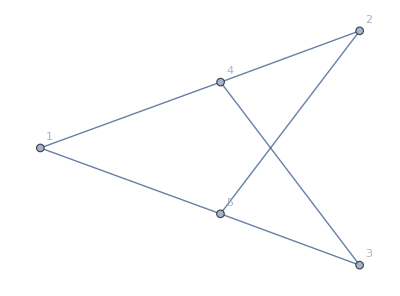
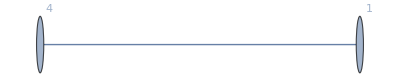
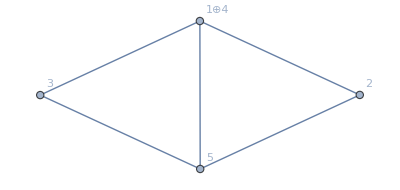
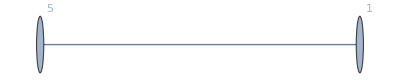
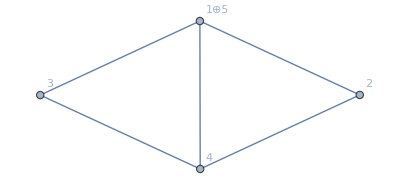
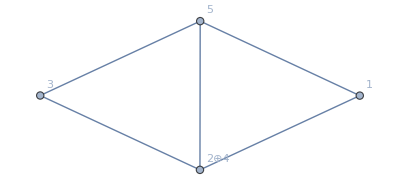
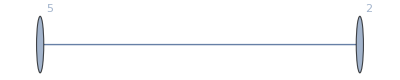
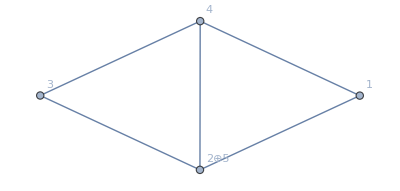
{-Graphics-,1 | (-Graphics- | {1,4} | {1<->4}
-Graphics- | {1⊕4,2,3,5} | {1⊕4<->5,2<->1⊕4,2<->5,3<->1⊕4,3<->5})
-1 | (-Graphics- | {1,5} | {1<->5}
-Graphics- | {1⊕5,2,3,4} | {1⊕5<->4,2<->4,2<->1⊕5,3<->4,3<->1⊕5})
1 | (-Graphics- | {2,4} | {2<->4}
-Graphics- | {1,2⊕4,3,5} | {1<->2⊕4,1<->5,2⊕4<->5,3<->2⊕4,3<->5})
-1 | (-Graphics- | {2,5} | {2<->5}
-Graphics- | {1,2⊕5,3,4} | {1<->4,1<->2⊕5,2⊕5<->4,3<->4,3<->2⊕5})
1 | (-Graphics- | {3,4} | {3<->4}
-Graphics- | {1,2,3⊕4,5} | {1<->3⊕4,1<->5,2<->3⊕4,2<->5,3⊕4<->5})
-1 | (-Graphics- | {3,5} | {3<->5}
-Graphics- | {1,2,3⊕5,4} | {1<->4,1<->3⊕5,2<->4,2<->3⊕5,3⊕5<->4})}

{{5<->1,1<->4,4<->3,3<->5},{5<->1,1<->4,4<->2,2<->5}}

```mathematica
(*The quadratic relation*)
flyingV=unlaman[5][[4]];
{flyingV//print,flyingV//contractGraphSigned//displayContractionsTable}
flyingV//FindFundamentalCycles
```

```mathematica
flyingVSub=toGoodGlobalLoops[flyingV]
```

{pz[1,4]→pZHold[1]+pZHold[2],pz[1,5]→-pZHold[1]-pZHold[2],pz[2,4]→-pZHold[2],pz[2,5]→pZHold[2],pz[3,4]→-pZHold[1],pz[3,5]→pZHold[1],z[2,5]→-z[1,4]+z[1,5]+z[2,4]+ZHold[2],z[3,5]→-z[1,4]+z[1,5]+z[3,4]+ZHold[1]}

```mathematica
(*Break apart the quadratic relation into individual pieces*)
{coeffs,J1s,J2s}=List@@quadJauto[flyingV]/.{a_. J1[x___]J2[y___]:>{a,J1[x],J2[y]},a_. J2[y___]:>{a,1,J2[y]}}//Transpose;
coeffs=coeffs;

{coeffs/coeffs[[2]]//Simplify,J1s,J2s}/.flyingVSub//Transpose//MatrixForm

coeffs=coeffs/coeffs[[2]]/.flyingVSub//Simplify
coeffs=coeffs/.{Exp[x___]:>Exp[Expand[x]]}/.{l[i_]ZHold[j_]:>lm[i].ZL[j]}
```

(-ⅇ^(-l[3] ZHold[1]-l[2] ZHold[2]) | 1 | J2[-Graphics-,{l[1],l[2],-l[1]-l[2]-l[4]},{-ZHold[1],-ZHold[2]}]
1 | 1 | J2[-Graphics-,{l[1],l[2],l[3]+l[4]},{ZHold[1],ZHold[2]}]
-ⅇ^(-l[3] ZHold[1]-l[2] ZHold[2]) | 1 | J2[-Graphics-,{l[1],l[3],-l[1]-l[3]-l[4]},{-ZHold[2],-ZHold[1]}]
1 | 1 | J2[-Graphics-,{l[1],l[3],l[2]+l[4]},{ZHold[2],ZHold[1]}]
-ⅇ^(-l[3] ZHold[1]-l[2] ZHold[2]-l[4] ZHold[2]) | 1 | J2[-Graphics-,{l[2],l[3],-l[2]-l[3]-l[4]},{ZHold[2],-ZHold[1]+ZHold[2]}]
ⅇ^(-((l[1]+l[2]+l[3]+l[4]) ZHold[2])) | 1 | J2[-Graphics-,{l[2],l[3],l[1]+l[4]},{-ZHold[2],ZHold[1]-ZHold[2]}])

{-ⅇ^(-l[3] ZHold[1]-l[2] ZHold[2]),1,-ⅇ^(-l[3] ZHold[1]-l[2] ZHold[2]),1,-ⅇ^(-l[3] ZHold[1]-(l[2]+l[4]) ZHold[2]),ⅇ^(-((l[1]+l[2]+l[3]+l[4]) ZHold[2]))}

{-ⅇ^(-ZHold[2,1] λ[2,1]-ZHold[2,2] λ[2,2]-ZHold[1,1] λ[3,1]-ZHold[1,2] λ[3,2]),1,-ⅇ^(-ZHold[2,1] λ[2,1]-ZHold[2,2] λ[2,2]-ZHold[1,1] λ[3,1]-ZHold[1,2] λ[3,2]),1,-ⅇ^(-ZHold[2,1] λ[2,1]-ZHold[2,2] λ[2,2]-ZHold[1,1] λ[3,1]-ZHold[1,2] λ[3,2]-ZHold[2,1] λ[4,1]-ZHold[2,2] λ[4,2]),ⅇ^(-ZHold[2,1] λ[1,1]-ZHold[2,2] λ[1,2]-ZHold[2,1] λ[2,1]-ZHold[2,2] λ[2,2]-ZHold[2,1] λ[3,1]-ZHold[2,2] λ[3,2]-ZHold[2,1] λ[4,1]-ZHold[2,2] λ[4,2])}

```mathematica
(*Make the J2s in terms of the proper 2-component variables*)
J2sSubbed=(J2s/.flyingVSub/.{l[i_]:>lm[i],ZHold[j_]:>ZL[j]});
(*Then replace all of the expressions with the bitriangleAns from the previous bootstrap result*)
J2sSubbed=(J2sSubbed/.{J2[bitri_,{l1__,l2__,l3__},{Z1__,Z2__}]:>(bitriangleAns/.{λ[1,i_]:>l1[[i]],λ[2,j_]:>l2[[j]],λ[3,k_]:>l3[[k]],ZHold[1,l_]:>Z1[[l]],ZHold[2,m_]:>Z2[[m]]})});
```

```mathematica
(*Expand flyingVboot so that it only expands up to order maxZ=2*)
flyingVboot=J2sSubbed.(coeffs/.{Exp[x___]:>Sum[x^ik/Factorial[ik],{ik,0,2}]});
ZList=Flatten[{ZL[1],ZL[2]}];
ar=CoefficientArrays[flyingVboot,ZList];
flyingVboot=Sum[mDR[ar[[i]],ZList,i-1],{i,1,2+1}]//Expand
```

0

```mathematica
(*[!] The answer is 0. This confirms that the quadratic identity for the flying V graph is satisfied.*)
```

#### The Flying V at z=0

```mathematica
bisymp[λ1_,λ2_,λ3_]:=1/24 symp[λ1,λ2+2λ3]symp[λ2,λ1+2λ3]
```

```mathematica
a=bisymp[lm[1],lm[2],lm[3]+lm[4]]-bisymp[lm[1],lm[2],-lm[1]-lm[2]-lm[4]]//Expand
b=bisymp[lm[1],lm[3],lm[2]+lm[4]]-bisymp[lm[1],lm[3],-lm[1]-lm[3]-lm[4]]//Expand
c=bisymp[lm[2],lm[3],lm[1]+lm[4]]-bisymp[lm[2],lm[3],-lm[2]-lm[3]-lm[4]]//Expand
a+b+c
```

-1/12 λ[1,2]^2 λ[2,1] λ[3,1]+1/12 λ[1,1] λ[1,2] λ[2,2] λ[3,1]+1/12 λ[1,2] λ[2,1] λ[2,2] λ[3,1]-1/12 λ[1,1] λ[2,2]^2 λ[3,1]+1/6 λ[1,2] λ[2,2] λ[3,1]^2+1/12 λ[1,1] λ[1,2] λ[2,1] λ[3,2]-1/12 λ[1,2] λ[2,1]^2 λ[3,2]-1/12 λ[1,1]^2 λ[2,2] λ[3,2]+1/12 λ[1,1] λ[2,1] λ[2,2] λ[3,2]-1/6 λ[1,2] λ[2,1] λ[3,1] λ[3,2]-1/6 λ[1,1] λ[2,2] λ[3,1] λ[3,2]+1/6 λ[1,1] λ[2,1] λ[3,2]^2+1/3 λ[1,2] λ[2,2] λ[3,1] λ[4,1]-1/6 λ[1,2] λ[2,1] λ[3,2] λ[4,1]-1/6 λ[1,1] λ[2,2] λ[3,2] λ[4,1]-1/6 λ[1,2] λ[2,1] λ[3,1] λ[4,2]-1/6 λ[1,1] λ[2,2] λ[3,1] λ[4,2]+1/3 λ[1,1] λ[2,1] λ[3,2] λ[4,2]

-1/12 λ[1,2]^2 λ[2,1] λ[3,1]+1/12 λ[1,1] λ[1,2] λ[2,2] λ[3,1]-1/6 λ[1,2] λ[2,1] λ[2,2] λ[3,1]+1/6 λ[1,1] λ[2,2]^2 λ[3,1]-1/12 λ[1,2] λ[2,2] λ[3,1]^2+1/12 λ[1,1] λ[1,2] λ[2,1] λ[3,2]+1/6 λ[1,2] λ[2,1]^2 λ[3,2]-1/12 λ[1,1]^2 λ[2,2] λ[3,2]-1/6 λ[1,1] λ[2,1] λ[2,2] λ[3,2]+1/12 λ[1,2] λ[2,1] λ[3,1] λ[3,2]+1/12 λ[1,1] λ[2,2] λ[3,1] λ[3,2]-1/12 λ[1,1] λ[2,1] λ[3,2]^2-1/6 λ[1,2] λ[2,2] λ[3,1] λ[4,1]+1/3 λ[1,2] λ[2,1] λ[3,2] λ[4,1]-1/6 λ[1,1] λ[2,2] λ[3,2] λ[4,1]-1/6 λ[1,2] λ[2,1] λ[3,1] λ[4,2]+1/3 λ[1,1] λ[2,2] λ[3,1] λ[4,2]-1/6 λ[1,1] λ[2,1] λ[3,2] λ[4,2]

1/6 λ[1,2]^2 λ[2,1] λ[3,1]-1/6 λ[1,1] λ[1,2] λ[2,2] λ[3,1]+1/12 λ[1,2] λ[2,1] λ[2,2] λ[3,1]-1/12 λ[1,1] λ[2,2]^2 λ[3,1]-1/12 λ[1,2] λ[2,2] λ[3,1]^2-1/6 λ[1,1] λ[1,2] λ[2,1] λ[3,2]-1/12 λ[1,2] λ[2,1]^2 λ[3,2]+1/6 λ[1,1]^2 λ[2,2] λ[3,2]+1/12 λ[1,1] λ[2,1] λ[2,2] λ[3,2]+1/12 λ[1,2] λ[2,1] λ[3,1] λ[3,2]+1/12 λ[1,1] λ[2,2] λ[3,1] λ[3,2]-1/12 λ[1,1] λ[2,1] λ[3,2]^2-1/6 λ[1,2] λ[2,2] λ[3,1] λ[4,1]-1/6 λ[1,2] λ[2,1] λ[3,2] λ[4,1]+1/3 λ[1,1] λ[2,2] λ[3,2] λ[4,1]+1/3 λ[1,2] λ[2,1] λ[3,1] λ[4,2]-1/6 λ[1,1] λ[2,2] λ[3,1] λ[4,2]-1/6 λ[1,1] λ[2,1] λ[3,2] λ[4,2]

0

### Example: Bootstrapping the TriTriangle

#### The TriTriangle

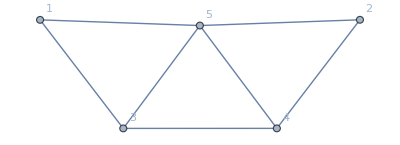

{{5<->1,1<->3,3<->4,4<->5},{5<->1,1<->3,3<->5},{4<->3,3<->1,1<->5,5<->2,2<->4}}

```mathematica
tritriangle=laman[5][[1]];
tritriangle//displayGraph
tritriangle//FindFundamentalCycles
```

```mathematica
(*The phase, converting I_{Gamma} to J_{Gamma}*)
Collect[canItoJ[tritriangle][[1]],λHold[___]]
```

-z[1,5] λHold[1]-z[2,5] λHold[2]+(z[1,3]-z[1,5]) λHold[3]+(z[1,3]-z[1,5]+z[3,4]) λHold[4]

```mathematica
(*Find symmetries*)
decomp=E^(-z[1,5] λHold[1]-z[2,5] λHold[2]+(z[1,3]-z[1,5]) λHold[3]+(z[1,3]-z[1,5]+z[3,4]) λHold[4])Jh[{λHold[1],λHold[2],λHold[3],λHold[4]},{z[1,3]-z[1,5]+z[3,4]+z[4,5],z[1,3]-z[1,5]+z[3,5],-z[1,3]+z[1,5]+z[2,4]-z[2,5]-z[3,4]}];

decomp/(decomp/.{1->2,2->1,3->4,4->3})/.toGoodGlobalLoops[tritriangle]//Simplify

(*The above ratio should be this signature at the bottom, reflecting swapping of edges in the graph*)
a1=tritriangle//EdgeList
a2=a1/.{1->2,2->1,3->4,4->3};
a2=Map[Sort,a2]
Signature[a1]/Signature[a2]
```

(ⅇ^(-ZHold[3] (λHold[3]+λHold[4])) Jh[{λHold[1],λHold[2],λHold[3],λHold[4]},{ZHold[1],ZHold[2],ZHold[3]}])/Jh[{λHold[2],λHold[1],λHold[4],λHold[3]},{ZHold[2]+ZHold[3],ZHold[1]+ZHold[3],-ZHold[3]}]

{1<->3,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5}

{2<->4,2<->5,1<->3,1<->5,3<->4,4<->5,3<->5}

-1

#### The TriTriangle Quadratic Relation

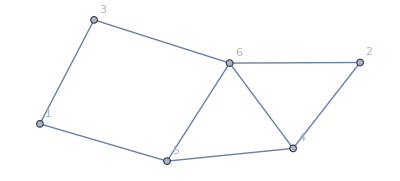

{{6<->3,3<->1,1<->5,5<->6},{6<->3,3<->1,1<->5,5<->4,4<->6},{4<->5,5<->1,1<->3,3<->6,6<->2,2<->4}}

```mathematica
(*The graph we will try to bootstrap the tritriangle with*)
sqtritri=unlaman[6][[4]]//CanonicalGraph;
sqtritri//displayGraph
sqtritri//FindFundamentalCycles
```

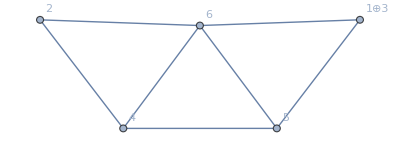
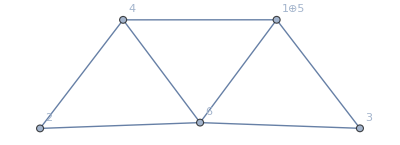
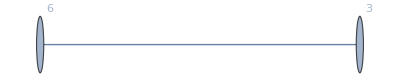
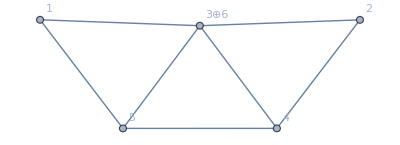
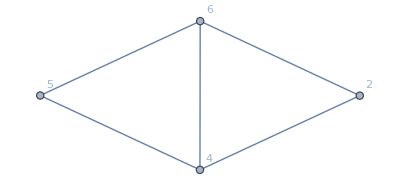
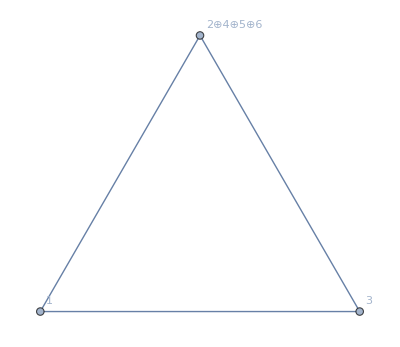
1 | (-Graphics- | {1,3} | {1<->3}
-Graphics- | {1⊕3,2,4,5,6} | {1⊕3<->5,2<->4,2<->6,1⊕3<->6,4<->5,4<->6,5<->6})
1 | (-Graphics- | {1,5} | {1<->5}
-Graphics- | {1⊕5,2,3,4,6} | {1⊕5<->3,2<->4,2<->6,3<->6,4<->1⊕5,4<->6,1⊕5<->6})
-1 | (-Graphics- | {3,6} | {3<->6}
-Graphics- | {1,2,3⊕6,4,5} | {1<->3⊕6,1<->5,2<->4,2<->3⊕6,4<->5,4<->3⊕6,5<->3⊕6})
-1 | (-Graphics- | {2,4,5,6} | {2<->4,2<->6,4<->5,4<->6,5<->6}
-Graphics- | {1,2⊕4⊕5⊕6,3} | {1<->3,1<->2⊕4⊕5⊕6,3<->2⊕4⊕5⊕6})

```mathematica
sqtritri//contractGraphSigned//displayContractionsTable
```

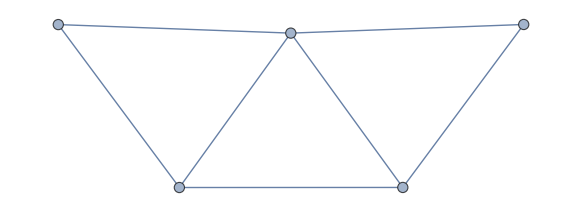
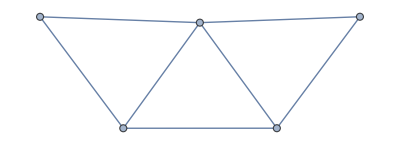
J1[-Graphics-,{l[2],l[5]-pZHold[1]-pZHold[2]+pZHold[3],l[4]},{ZHold[2]+ZHold[3],ZHold[1]+ZHold[3]}] J2[-Graphics-,{l[1],-l[1]-l[3]},{-ZHold[3]}]-J2[-Graphics-,{l[2],l[1],l[4],l[5]},{ZHold[1]+ZHold[3],ZHold[2]+ZHold[3],-ZHold[3]}]+J2[-Graphics-,{l[2],l[1]+l[3],l[4],l[5]},{ZHold[1]+ZHold[3],ZHold[2]+ZHold[3],-ZHold[3]}]+ⅇ^(-l[4] ZHold[3]-l[5] ZHold[3]) J2[-Graphics-,{l[3],l[2],l[1]+l[5],l[4]},{ZHold[2],ZHold[1],ZHold[3]}]

```mathematica
(*The quadratic relation*)
reducedQuadAuto[sqtritri]
```

#### The TriTriangle Bootstrap

```mathematica
(*An ansatz for the tritriangle expression (at order zero in z)*)
TriTriBootNoZ[{l11_,l12_},{l21_,l22_},{l31_,l32_},{l41_,l42_},maxL_]:=Sum[If[i+j+k+l+m+n+s+t==6,threeLoop[i,j,k,l,m,n,s,t]mP[l11,i]mP[l12,j]mP[l21,k]mP[l22,l]mP[l31,m]mP[l32,n]mP[l41,s]mP[l42,t],0],{i,0,maxL},{j,0,maxL-i},{k,0,maxL-i-j},{l,0,maxL-i-j-k},{m,0,maxL-i-j-k-l},{n,0,maxL-i-j-k-l-m},{s,0,maxL-i-j-k-l-m-n},{t,0,maxL-i-j-k-l-m-s}]

(*A taylor series expansion for the bitriangle*)
TriTriBootNoZList[maxL_]:=DeleteCases[Flatten[Table[If[i+j+k+l+m+n+s+t==6,threeLoop[i,j,k,l,m,n,s,t],-1],{i,0,maxL},{j,0,maxL-i},{k,0,maxL-i-j},{l,0,maxL-i-j-k},{m,0,maxL-i-j-k-l},{n,0,maxL-i-j-k-l-m},{s,0,maxL-i-j-k-l-m-n},{t,0,maxL-i-j-k-l-m-s}]],-1]
```

```mathematica
{coeffs,J1s,J2s}=List@@quadJauto[sqtritri]/.{a_. J1[x___]J2[y___]:>{a,J1[x],J2[y]},a_. J2[y___]:>{a,1,J2[y]}}//Transpose;
coeffs=coeffs/.{Exp[x___]:>Exp[Expand[x]]}/.{l[i_]ZHold[j_]:>lm[i].ZL[j]};

{coeffs,J1s,J2s}//MatrixForm
```

(ⅇ^(-l[1] z[1,3]+l[4] z[2,4]+l[5] z[2,4]-l[2] z[2,6]-l[4] z[2,6]-l[5] z[2,6]-l[1] z[3,6]-l[3] z[3,6]+l[5] z[4,5]) | -ⅇ^(-l[1] z[1,3]+l[4] z[2,4]+l[5] z[2,4]-l[2] z[2,6]-l[4] z[2,6]-l[5] z[2,6]-l[1] z[3,6]-l[3] z[3,6]+l[5] z[4,5]) | ⅇ^(-l[1] z[1,3]+l[4] z[2,4]+l[5] z[2,4]-l[2] z[2,6]-l[4] z[2,6]-l[5] z[2,6]-l[1] z[3,6]-l[3] z[3,6]+l[5] z[4,5]) | ⅇ^(-l[1] z[1,3]-l[4] z[1,3]-l[5] z[1,3]+l[4] z[1,5]+l[5] z[1,5]-l[2] z[2,6]-l[1] z[3,6]-l[3] z[3,6]-l[4] z[3,6]-l[5] z[3,6]-l[4] z[4,5])
J1[-Graphics-,{l[2],l[5]-pz[1,5],l[4]},{z[2,4]-z[2,6]+z[4,6],z[2,4]-z[2,6]+z[4,5]+z[5,6]}] | 1 | 1 | 1
J2[-Graphics-,{l[1],-l[1]-l[3]},{-z[1,3]+z[1,5]-z[2,4]+z[2,6]-z[3,6]-z[4,5]}] | J2[-Graphics-,{l[2],l[1],l[4],l[5]},{z[2,4]-z[2,6]+z[4,5]+z[5,6],z[2,4]-z[2,6]+z[4,6],-z[1,3]+z[1,5]-z[2,4]+z[2,6]-z[3,6]-z[4,5]}] | J2[-Graphics-,{l[2],l[1]+l[3],l[4],l[5]},{z[2,4]-z[2,6]+z[4,5]+z[5,6],z[2,4]-z[2,6]+z[4,6],-z[1,3]+z[1,5]-z[2,4]+z[2,6]-z[3,6]-z[4,5]}] | J2[-Graphics-,{l[3],l[2],l[1]+l[5],l[4]},{-z[1,3]+z[1,5]-z[3,6]-z[4,5]+z[4,6],-z[1,3]+z[1,5]-z[3,6]+z[5,6],z[1,3]-z[1,5]+z[2,4]-z[2,6]+z[3,6]+z[4,5]}])

```mathematica
goodLoops=toGoodGlobalLoops[sqtritri]
divcof=coeffs/(coeffs[[1]])/.goodLoops//Simplify
```

{pz[1,3]→-pZHold[1]-pZHold[2]+pZHold[3],pz[1,5]→pZHold[1]+pZHold[2]-pZHold[3],pz[2,4]→pZHold[3],pz[2,6]→-pZHold[3],pz[3,6]→-pZHold[1]-pZHold[2]+pZHold[3],pz[4,5]→-pZHold[2]+pZHold[3],pz[4,6]→pZHold[2],pz[5,6]→pZHold[1],z[2,4]→-z[1,3]+z[1,5]+z[2,6]-z[3,6]-z[4,5]+ZHold[3],z[4,6]→z[1,3]-z[1,5]+z[3,6]+z[4,5]+ZHold[2],z[5,6]→z[1,3]-z[1,5]+z[3,6]+ZHold[1]}

{1,-1,1,ⅇ^(-((l[4]+l[5]) ZHold[3]))}

```mathematica
(*The ansatz we want to bootstrap*)
ansatz=TriTriBootNoZ[lm[1],lm[2],lm[3],lm[4],6];
```

```mathematica
(*Impose SU(2) relation*)
SU21=λ[1,1]D[ansatz,λ[1,2]]+λ[2,1]D[ansatz,λ[2,2]]+λ[3,1]D[ansatz,λ[3,2]]+λ[4,1]D[ansatz,λ[4,2]];
solsSU21=seriesToLinEq[SU21,Flatten[Table[lm[i],{i,1,4}]],TriTriBootNoZList[6]][[1]];
ansatz2=ansatz/.solsSU21;
ansatz2//Variables;
```

```mathematica
(*Impose the second SU(2) relation*)
SU22=λ[1,2]D[ansatz2,λ[1,1]]+λ[2,2]D[ansatz2,λ[2,1]]+λ[3,2]D[ansatz2,λ[3,1]]+λ[4,2]D[ansatz2,λ[4,1]];
solsSU22=seriesToLinEq[SU22,Flatten[Table[lm[i],{i,1,4}]],TriTriBootNoZList[6]][[1]];
ansatz3=ansatz2/.solsSU22;
ansatz3//Variables
```

{threeLoop[0,3,3,0,0,0,0,0],λ[1,2],λ[2,1],λ[1,1],λ[2,2],threeLoop[0,3,2,0,1,0,0,0],λ[3,1],threeLoop[0,2,2,1,1,0,0,0],threeLoop[0,3,1,0,2,0,0,0],threeLoop[0,2,1,1,2,0,0,0],threeLoop[0,1,1,2,2,0,0,0],threeLoop[0,3,0,0,3,0,0,0],threeLoop[0,2,0,1,3,0,0,0],threeLoop[0,1,0,2,3,0,0,0],threeLoop[0,0,0,3,3,0,0,0],λ[3,2],threeLoop[0,3,2,0,0,0,1,0],λ[4,1],threeLoop[0,2,2,1,0,0,1,0],threeLoop[0,3,1,0,1,0,1,0],threeLoop[0,2,1,1,1,0,1,0],threeLoop[0,1,1,2,1,0,1,0],threeLoop[0,3,0,0,2,0,1,0],threeLoop[0,2,0,1,2,0,1,0],threeLoop[0,1,0,2,2,0,1,0],threeLoop[0,0,0,3,2,0,1,0],threeLoop[0,2,2,0,0,1,1,0],threeLoop[0,2,1,0,1,1,1,0],threeLoop[0,1,1,1,1,1,1,0],threeLoop[0,2,0,0,2,1,1,0],threeLoop[0,1,0,1,2,1,1,0],threeLoop[0,0,0,2,2,1,1,0],threeLoop[0,3,1,0,0,0,2,0],threeLoop[0,2,1,1,0,0,2,0],threeLoop[0,1,1,2,0,0,2,0],threeLoop[0,3,0,0,1,0,2,0],threeLoop[0,2,0,1,1,0,2,0],threeLoop[0,1,0,2,1,0,2,0],threeLoop[0,0,0,3,1,0,2,0],threeLoop[0,2,1,0,0,1,2,0],threeLoop[0,1,1,1,0,1,2,0],threeLoop[0,2,0,0,1,1,2,0],threeLoop[0,1,0,1,1,1,2,0],threeLoop[0,0,0,2,1,1,2,0],threeLoop[0,1,1,0,0,2,2,0],threeLoop[0,1,0,0,1,2,2,0],threeLoop[0,0,0,1,1,2,2,0],threeLoop[0,3,0,0,0,0,3,0],threeLoop[0,2,0,1,0,0,3,0],threeLoop[0,1,0,2,0,0,3,0],threeLoop[0,0,0,3,0,0,3,0],threeLoop[0,2,0,0,0,1,3,0],threeLoop[0,1,0,1,0,1,3,0],threeLoop[0,0,0,2,0,1,3,0],threeLoop[0,1,0,0,0,2,3,0],threeLoop[0,0,0,1,0,2,3,0],threeLoop[0,0,0,0,0,3,3,0],λ[4,2]}

```mathematica
(*The SU(2) invariant quantity*)
TriTriBootNoZSU2[l1_,l2_,l3_,l4_,len_]:=TriTriBootNoZ[l1,l2,l3,l4,len]/.solsSU21/.solsSU22;
```

```mathematica
(*Replace all of the tritriangles with the SU(2) invariant ansatz*)
tritris=((J2s[[2;;4]]/.{l[i_]:>lm[i],ZHold[j_]:>ZL[j]})/.{J2[tritri_,{l1__,l2__,l3__,l4__},{Z1__,Z2__,Z3__}]:>TriTriBootNoZSU2[l1,l2,l3,l4,6]});
```

```mathematica
(*The bitriangle x triangle source function for the tritriangle bootstrap*)
({J1s[[1]],J2s[[1]]}/.goodLoops)/.{pZHold[1]->0,pZHold[2]->0}
```

{J1[-Graphics-,{l[2],l[5]+pZHold[3],l[4]},{ZHold[2]+ZHold[3],ZHold[1]+ZHold[3]}],J2[-Graphics-,{l[1],-l[1]-l[3]},{-ZHold[3]}]}

```mathematica
(*The bitriangle who is Acting*)
ActWithMe=bitriangleAns/.{λ[1,i_]:>λ[2,i],λ[2,j_]:>λ[5,j],λ[3,k_]:>λ[4,k],ZHold[1,l_]:>ZHold[2,l]+ZHold[3,l],ZHold[2,m_]:>ZHold[1,m]+ZHold[3,m]};

(*The bitriangle getting Acted on in the quadratic relation you choose*)
triMax=4;
ActOnMe=JtriExact[lm[1],-lm[1]-lm[3],-ZL[3],triMax];

BitriTri=seriesToOperator[ActWithMe,{lm[5]},{{1,ZL[3]}},ActOnMe];
```

```mathematica
nocoeffs={BitriTri,tritris}//Flatten;
bootstrapMe=nocoeffs.divcof/.{ZHold[i_,j_]:>0,ZHold[k_]:>0};
```

```mathematica
varList=Flatten[{Table[lm[i],{i,1,5}]}]
```

{λ[1,1],λ[1,2],λ[2,1],λ[2,2],λ[3,1],λ[3,2],λ[4,1],λ[4,2],λ[5,1],λ[5,2]}

```mathematica
(*Solve the bootstrap equation*)
sols=seriesToLinEq[bootstrapMe,varList,Flatten[{TriTriBootNoZList[6],tritriCo}]][[1]];
```

```mathematica
(*There are two variables left! There should only be one, an overall scale!*)
ans=TriTriBootNoZSU2[lm[1],lm[2],lm[3],lm[4],6]/.sols//Expand;
(ans//Variables)/.{λ[___]:>Sequence[],ZHold[___]:>Sequence[]}
```

{threeLoop[0,2,2,1,1,0,0,0],tritriCo}

```mathematica
(*The symmetry equation is already enforced, so it won't help us.*)
ans+(ans/.{λ[1,i_]:>λ[2,i],λ[2,j_]:>λ[1,j],λ[3,k_]:>λ[4,k],λ[4,l_]:>λ[3,l]})//Expand
```

0

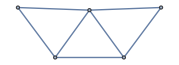
```mathematica
g=-Graphics-//CanonicalGraph
```

-Graphics-

```mathematica
g//displayGraph
```

-Graphics-

#### One more equation

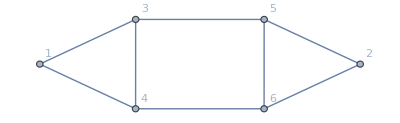

{{6<->4,4<->1,1<->3,3<->5,5<->6},{4<->1,1<->3,3<->4},{6<->4,4<->1,1<->3,3<->5,5<->2,2<->6}}

```mathematica
(*This graph also generates a quadratic relation*)
extraGraph=unlaman[6][[3]];
extraGraph//displayGraph
extraGraph//FindFundamentalCycles
```

```mathematica
reducedQuadAuto[extraGraph]
dat=List@@reducedQuadAuto[extraGraph]/.{J1[___]:>1,J2[___]:>1,Exp[x___]:>Exp[Collect[Expand[x],l[___]]]};
dat//MatrixForm
```

-J1[-Graphics-,{l[2],l[1]+l[3]+l[4]+l[5]-pZHold[1]-pZHold[3]},{ZHold[1]-ZHold[3]}] J2[-Graphics-,{l[1],-l[1]-l[3]-l[4],l[3]},{ZHold[2],ZHold[1]}]+ⅇ^(l[1] ZHold[1]+l[4] ZHold[1]+l[3] (ZHold[1]-ZHold[2])+l[5] (ZHold[1]-ZHold[2])+l[2] (-ZHold[2]+ZHold[3])) J1[-Graphics-,{l[1],l[2]+l[3]+l[5]+pZHold[1]+pZHold[3]},{ZHold[2]}] J2[-Graphics-,{l[1]+l[3]+l[4],l[2],l[5]},{ZHold[1]-ZHold[2],-ZHold[2]+ZHold[3]}]-ⅇ^(l[1] ZHold[1]+l[3] ZHold[1]+l[4] ZHold[1]+l[5] ZHold[1]) J2[-Graphics-,{l[1],l[2],l[3],l[5]},{ZHold[1],ZHold[2],-ZHold[3]}]+ⅇ^(l[1] ZHold[1]+l[3] ZHold[1]+l[4] ZHold[1]+l[5] ZHold[1]+l[2] ZHold[3]) J2[-Graphics-,{l[1],l[2],l[4],-l[1]-l[2]-l[3]-l[4]-l[5]},{-ZHold[1],-ZHold[2],ZHold[3]}]

```mathematica
dat/dat[[3]]//Simplify//MatrixForm
```

(ⅇ^(-((l[1]+l[3]+l[4]+l[5]) ZHold[1]))
-ⅇ^(-((l[3]+l[5]) ZHold[2])+l[2] (-ZHold[2]+ZHold[3]))
1
-ⅇ^(l[2] ZHold[3]))

```mathematica
{coeffs2,J1s2,J2s2}=List@@quadJauto[extraGraph]/.{a_. J1[x___]J2[y___]:>{a,J1[x],J2[y]},a_. J2[y___]:>{a,1,J2[y]}}//Transpose;
coeffs2=coeffs2/.{Exp[x___]:>Exp[Expand[x]]}/.{l[i_]ZHold[j_]:>lm[i].ZL[j]};

{coeffs2/(coeffs2[[1]]),J1s2,J2s2}//MatrixForm
```

(1 | -ⅇ^(l[1] z[1,3]+l[4] z[1,3]-l[1] z[1,4]-l[4] z[1,4]-l[2] z[2,5]+l[2] z[2,6]-l[2] z[3,4]-l[3] z[3,4]-l[5] z[3,4]+l[1] z[3,5]+l[2] z[3,5]+l[3] z[3,5]+l[4] z[3,5]+l[5] z[3,5]-l[1] z[4,6]-l[2] z[4,6]-l[3] z[4,6]-l[4] z[4,6]-l[5] z[4,6]+l[1] z[5,6]+l[3] z[5,6]+l[4] z[5,6]+l[5] z[5,6]) | ⅇ^(l[1] z[1,3]+l[3] z[1,3]+l[4] z[1,3]+l[5] z[1,3]-l[1] z[1,4]-l[3] z[1,4]-l[4] z[1,4]-l[5] z[1,4]+l[1] z[3,5]+l[3] z[3,5]+l[4] z[3,5]+l[5] z[3,5]-l[1] z[4,6]-l[3] z[4,6]-l[4] z[4,6]-l[5] z[4,6]+l[1] z[5,6]+l[3] z[5,6]+l[4] z[5,6]+l[5] z[5,6]) | -ⅇ^(l[1] z[1,3]+l[2] z[1,3]+l[3] z[1,3]+l[4] z[1,3]+l[5] z[1,3]-l[1] z[1,4]-l[2] z[1,4]-l[3] z[1,4]-l[4] z[1,4]-l[5] z[1,4]-l[2] z[2,5]+l[2] z[2,6]+l[1] z[3,5]+l[2] z[3,5]+l[3] z[3,5]+l[4] z[3,5]+l[5] z[3,5]-l[1] z[4,6]-l[2] z[4,6]-l[3] z[4,6]-l[4] z[4,6]-l[5] z[4,6]+l[1] z[5,6]+l[3] z[5,6]+l[4] z[5,6]+l[5] z[5,6])
J1[-Graphics-,{l[2],l[1]+l[3]+l[4]+l[5]-pz[3,5]},{z[2,5]-z[2,6]+z[5,6]}] | J1[-Graphics-,{l[1],l[2]+l[3]+l[5]+pz[3,5]},{z[1,3]-z[1,4]+z[3,4]}] | 1 | 1
J2[-Graphics-,{l[1],-l[1]-l[3]-l[4],l[3]},{z[1,3]-z[1,4]+z[3,4],z[1,3]-z[1,4]+z[3,5]-z[4,6]+z[5,6]}] | J2[-Graphics-,{l[1]+l[3]+l[4],l[2],l[5]},{-z[3,4]+z[3,5]-z[4,6]+z[5,6],-z[2,5]+z[2,6]-z[3,4]+z[3,5]-z[4,6]}] | J2[-Graphics-,{l[1],l[2],l[3],l[5]},{z[1,3]-z[1,4]+z[3,5]-z[4,6]+z[5,6],z[1,3]-z[1,4]+z[3,4],-z[1,3]+z[1,4]+z[2,5]-z[2,6]-z[3,5]+z[4,6]}] | J2[-Graphics-,{l[1],l[2],l[4],-l[1]-l[2]-l[3]-l[4]-l[5]},{-z[1,3]+z[1,4]-z[3,5]+z[4,6]-z[5,6],-z[1,3]+z[1,4]-z[3,4],z[1,3]-z[1,4]-z[2,5]+z[2,6]+z[3,5]-z[4,6]}])

```mathematica
goodLoops2=toGoodGlobalLoops[extraGraph]
{coeffs2/(coeffs2[[1]]),J1s2,J2s2}/.goodLoops2//Simplify//MatrixForm
```

{pz[1,3]→pZHold[1]+pZHold[2]+pZHold[3],pz[1,4]→-pZHold[1]-pZHold[2]-pZHold[3],pz[2,5]→-pZHold[3],pz[2,6]→pZHold[3],pz[3,4]→pZHold[2],pz[3,5]→pZHold[1]+pZHold[3],pz[4,6]→-pZHold[1]-pZHold[3],pz[5,6]→pZHold[1],z[2,6]→-z[1,3]+z[1,4]+z[2,5]-z[3,5]+z[4,6]+ZHold[3],z[3,4]→-z[1,3]+z[1,4]+ZHold[2],z[5,6]→-z[1,3]+z[1,4]-z[3,5]+z[4,6]+ZHold[1]}

(1 | -ⅇ^(l[1] ZHold[1]+l[4] ZHold[1]+l[5] ZHold[1]+l[3] (ZHold[1]-ZHold[2])-l[2] ZHold[2]-l[5] ZHold[2]+l[2] ZHold[3]) | ⅇ^((l[1]+l[3]+l[4]+l[5]) ZHold[1]) | -ⅇ^(l[1] ZHold[1]+l[3] ZHold[1]+l[4] ZHold[1]+l[5] ZHold[1]+l[2] ZHold[3])
J1[-Graphics-,{l[2],l[1]+l[3]+l[4]+l[5]-pZHold[1]-pZHold[3]},{ZHold[1]-ZHold[3]}] | J1[-Graphics-,{l[1],l[2]+l[3]+l[5]+pZHold[1]+pZHold[3]},{ZHold[2]}] | 1 | 1
J2[-Graphics-,{l[1],-l[1]-l[3]-l[4],l[3]},{ZHold[2],ZHold[1]}] | J2[-Graphics-,{l[1]+l[3]+l[4],l[2],l[5]},{ZHold[1]-ZHold[2],-ZHold[2]+ZHold[3]}] | J2[-Graphics-,{l[1],l[2],l[3],l[5]},{ZHold[1],ZHold[2],-ZHold[3]}] | J2[-Graphics-,{l[1],l[2],l[4],-l[1]-l[2]-l[3]-l[4]-l[5]},{-ZHold[1],-ZHold[2],ZHold[3]}])

```mathematica
(*
Compute the action of triangles on the bitriangles (we bootstrapped that result previously);
Or rather, prepare for the calculation;
*)
triMax=4;
ActWithMe21=JtriExact[lm[2],lm[1]+lm[3]+lm[4]+lm[5],ZL[1]-ZL[3],triMax];
ActWithMe21=(Series[ActWithMe21/.{ZHold[i_,j_]:>e ZHold[i,j]},{e,0,3}]//Normal)/.{e->1};
ActWithMe22=JtriExact[lm[1],lm[2]+lm[3]+lm[5],ZL[2],triMax];
ActWithMe22=(Series[ActWithMe22/.{ZHold[i_,j_]:>e ZHold[i,j]},{e,0,3}]//Normal)/.{e->1};

ActOnMe21=bitriangleAns/.{λ[2,j_]:>-λ[1,j]-λ[3,j]-λ[4,j],ZHold[1,l_]:>ZHold[2,l],ZHold[2,m_]:>ZHold[1,m]};
ActOnMe22=bitriangleAns/.{λ[1,i_]:>λ[1,i]+λ[3,i]+λ[4,i],λ[3,k_]:>λ[5,k],ZHold[1,l_]:>ZHold[1,l]-ZHold[2,l],ZHold[2,m_]:>-ZHold[2,m]+ZHold[3,m]};
```

```mathematica
(*The first Triangle acting on Bitriangle*)
TriBitri1=seriesToOperator[ActWithMe21,{lm[5]},{{-1,ZL[1]}},ActOnMe21];
```

```mathematica
(*The second Triangle acting on a Bitriangle*)
TriBitri2=seriesToOperator[ActWithMe22,{lm[3],lm[5]},{{1,ZL[1]},{1,ZL[3]}},ActOnMe22];
```

```mathematica
(*We have two tritriangle terms in the quadratic relation*)
tritris2={
ans/.{λ[4,l_]:>λ[5,l]},
ans/.{λ[3,k_]:>λ[4,k],λ[4,l_]:>-λ[1,l]-λ[2,l]-λ[3,l]-λ[4,l]-λ[5,l]}
};
```

```mathematica
(*I will just arbitrarily weight each of the graphs with one of these coefficients, which should turn out to be signs*)
divcof2s={un1,un2,un3,un4};

(*The graph expressions*)
nocoeffs2=Flatten[{TriBitri1,TriBitri2,tritris2}];

(*Fold the results together*)
bootstrapMe2=nocoeffs2.divcof2s/.{ZHold[i_,j_]:>0,ZHold[k_]:>0}//Expand;
```

{tritriCo,un2,un4,un3,threeLoop[0,2,2,1,1,0,0,0],un1}

```mathematica
(*We don't even have to be fancy and use seriesToLinEq, we can just read off the coefficients that fix bootstrapMe2 ourselves*)
rep={un1->-un3,un2->1/3 (3un3),threeLoop[0,2,2,1,1,0,0,0]->tritriCo/288,un4->-un3}
bootstrapMe2/.rep
```

{un1→-un3,un2→un3,threeLoop[0,2,2,1,1,0,0,0]→tritriCo/288,un4→-un3}

0

```mathematica
tritriangleAns=ans/.rep/.tritriCo->1
```

-1/864 λ[1,2]^3 λ[2,1]^3+1/288 λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[2,2]-1/288 λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2]^2+1/864 λ[1,1]^3 λ[2,2]^3-1/288 λ[1,2]^3 λ[2,1]^2 λ[3,1]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]+1/288 λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,1]-1/288 λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,1]-1/144 λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]+1/288 λ[1,1]^2 λ[2,2]^3 λ[3,1]+1/96 λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]^2-1/96 λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1]^2-1/288 λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]^2+1/288 λ[1,1] λ[2,2]^3 λ[3,1]^2-1/96 λ[1,2] λ[2,2]^2 λ[3,1]^3+1/288 λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,2]-1/288 λ[1,2]^2 λ[2,1]^3 λ[3,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,2]+1/144 λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]+1/288 λ[1,1]^3 λ[2,2]^2 λ[3,2]-1/288 λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,2]-1/96 λ[1,2]^2 λ[2,1]^2 λ[3,1] λ[3,2]+1/144 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]+1/96 λ[1,1]^2 λ[2,2]^2 λ[3,1] λ[3,2]-1/144 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]+1/48 λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]+1/96 λ[1,1] λ[2,2]^2 λ[3,1]^2 λ[3,2]+1/96 λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2]^2-1/288 λ[1,2] λ[2,1]^3 λ[3,2]^2-1/96 λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2]^2+1/288 λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2]^2-1/96 λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]^2-1/48 λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2+1/96 λ[1,1] λ[2,1]^2 λ[3,2]^3-1/288 λ[1,2]^3 λ[2,1]^2 λ[4,1]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[4,1]+1/288 λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[4,1]-1/288 λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[4,1]-1/144 λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[4,1]+1/288 λ[1,1]^2 λ[2,2]^3 λ[4,1]-1/144 λ[1,2]^3 λ[2,1] λ[3,1] λ[4,1]+1/144 λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1] λ[4,1]+1/48 λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1] λ[4,1]-1/48 λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1] λ[4,1]-1/144 λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1] λ[4,1]+1/144 λ[1,1] λ[2,2]^3 λ[3,1] λ[4,1]+1/96 λ[1,2]^2 λ[2,2] λ[3,1]^2 λ[4,1]-1/32 λ[1,2] λ[2,2]^2 λ[3,1]^2 λ[4,1]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[3,2] λ[4,1]-1/96 λ[1,2]^2 λ[2,1]^2 λ[3,2] λ[4,1]-1/144 λ[1,1]^2 λ[1,2] λ[2,2] λ[3,2] λ[4,1]+1/144 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2] λ[4,1]+1/96 λ[1,1]^2 λ[2,2]^2 λ[3,2] λ[4,1]-1/144 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,2] λ[4,1]-1/48 λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2] λ[4,1]+1/24 λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2] λ[4,1]+1/48 λ[1,1] λ[2,2]^2 λ[3,1] λ[3,2] λ[4,1]+1/48 λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2] λ[4,1]+1/48 λ[1,1] λ[1,2] λ[2,1] λ[3,2]^2 λ[4,1]-1/96 λ[1,2] λ[2,1]^2 λ[3,2]^2 λ[4,1]-1/96 λ[1,1]^2 λ[2,2] λ[3,2]^2 λ[4,1]-1/48 λ[1,1] λ[2,1] λ[2,2] λ[3,2]^2 λ[4,1]-1/48 λ[1,2] λ[2,1] λ[3,1] λ[3,2]^2 λ[4,1]-1/48 λ[1,1] λ[2,2] λ[3,1] λ[3,2]^2 λ[4,1]+1/48 λ[1,1] λ[2,1] λ[3,2]^3 λ[4,1]-1/288 λ[1,2]^3 λ[2,1] λ[4,1]^2+1/288 λ[1,1] λ[1,2]^2 λ[2,2] λ[4,1]^2+1/96 λ[1,2]^2 λ[2,1] λ[2,2] λ[4,1]^2-1/96 λ[1,1] λ[1,2] λ[2,2]^2 λ[4,1]^2+1/32 λ[1,2]^2 λ[2,2] λ[3,1] λ[4,1]^2-1/96 λ[1,2] λ[2,2]^2 λ[3,1] λ[4,1]^2-1/96 λ[1,2]^2 λ[2,1] λ[3,2] λ[4,1]^2-1/48 λ[1,1] λ[1,2] λ[2,2] λ[3,2] λ[4,1]^2+1/48 λ[1,2] λ[2,1] λ[2,2] λ[3,2] λ[4,1]^2-1/96 λ[1,1] λ[2,2]^2 λ[3,2] λ[4,1]^2+1/16 λ[1,2] λ[2,2] λ[3,1] λ[3,2] λ[4,1]^2-1/96 λ[1,2] λ[2,1] λ[3,2]^2 λ[4,1]^2-5/96 λ[1,1] λ[2,2] λ[3,2]^2 λ[4,1]^2+1/96 λ[1,2]^2 λ[2,2] λ[4,1]^3+1/48 λ[1,2] λ[2,2] λ[3,2] λ[4,1]^3+1/288 λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[4,2]-1/288 λ[1,2]^2 λ[2,1]^3 λ[4,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[4,2]+1/144 λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[4,2]+1/288 λ[1,1]^3 λ[2,2]^2 λ[4,2]-1/288 λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[4,2]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1] λ[4,2]-1/96 λ[1,2]^2 λ[2,1]^2 λ[3,1] λ[4,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1] λ[4,2]+1/144 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1] λ[4,2]+1/96 λ[1,1]^2 λ[2,2]^2 λ[3,1] λ[4,2]-1/144 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1] λ[4,2]+1/96 λ[1,2]^2 λ[2,1] λ[3,1]^2 λ[4,2]-1/48 λ[1,1] λ[1,2] λ[2,2] λ[3,1]^2 λ[4,2]+1/48 λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2 λ[4,2]+1/96 λ[1,1] λ[2,2]^2 λ[3,1]^2 λ[4,2]-1/48 λ[1,2] λ[2,2] λ[3,1]^3 λ[4,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,1] λ[3,2] λ[4,2]+1/48 λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2] λ[4,2]-1/144 λ[1,2] λ[2,1]^3 λ[3,2] λ[4,2]+1/144 λ[1,1]^3 λ[2,2] λ[3,2] λ[4,2]-1/48 λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2] λ[4,2]+1/144 λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2] λ[4,2]-1/48 λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2] λ[4,2]+1/48 λ[1,1]^2 λ[2,2] λ[3,1] λ[3,2] λ[4,2]-1/24 λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2] λ[4,2]+1/48 λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2] λ[4,2]+1/48 λ[1,1] λ[2,2] λ[3,1]^2 λ[3,2] λ[4,2]-1/96 λ[1,1]^2 λ[2,1] λ[3,2]^2 λ[4,2]+1/32 λ[1,1] λ[2,1]^2 λ[3,2]^2 λ[4,2]-1/48 λ[1,1] λ[2,1] λ[3,1] λ[3,2]^2 λ[4,2]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[4,1] λ[4,2]-1/96 λ[1,2]^2 λ[2,1]^2 λ[4,1] λ[4,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,2] λ[4,1] λ[4,2]+1/96 λ[1,1]^2 λ[2,2]^2 λ[4,1] λ[4,2]-1/48 λ[1,2]^2 λ[2,1] λ[3,1] λ[4,1] λ[4,2]-1/24 λ[1,1] λ[1,2] λ[2,2] λ[3,1] λ[4,1] λ[4,2]+1/48 λ[1,1] λ[2,2]^2 λ[3,1] λ[4,1] λ[4,2]-1/16 λ[1,2] λ[2,2] λ[3,1]^2 λ[4,1] λ[4,2]+1/24 λ[1,1] λ[1,2] λ[2,1] λ[3,2] λ[4,1] λ[4,2]-1/48 λ[1,2] λ[2,1]^2 λ[3,2] λ[4,1] λ[4,2]+1/48 λ[1,1]^2 λ[2,2] λ[3,2] λ[4,1] λ[4,2]-1/24 λ[1,2] λ[2,1] λ[3,1] λ[3,2] λ[4,1] λ[4,2]+1/24 λ[1,1] λ[2,2] λ[3,1] λ[3,2] λ[4,1] λ[4,2]+1/16 λ[1,1] λ[2,1] λ[3,2]^2 λ[4,1] λ[4,2]-1/96 λ[1,2]^2 λ[2,1] λ[4,1]^2 λ[4,2]-1/48 λ[1,1] λ[1,2] λ[2,2] λ[4,1]^2 λ[4,2]-1/48 λ[1,2] λ[2,2] λ[3,1] λ[4,1]^2 λ[4,2]-1/48 λ[1,2] λ[2,1] λ[3,2] λ[4,1]^2 λ[4,2]-1/48 λ[1,1] λ[2,2] λ[3,2] λ[4,1]^2 λ[4,2]-1/288 λ[1,1]^2 λ[1,2] λ[2,1] λ[4,2]^2+1/96 λ[1,1] λ[1,2] λ[2,1]^2 λ[4,2]^2+1/288 λ[1,1]^3 λ[2,2] λ[4,2]^2-1/96 λ[1,1]^2 λ[2,1] λ[2,2] λ[4,2]^2+1/48 λ[1,1] λ[1,2] λ[2,1] λ[3,1] λ[4,2]^2+1/96 λ[1,2] λ[2,1]^2 λ[3,1] λ[4,2]^2+1/96 λ[1,1]^2 λ[2,2] λ[3,1] λ[4,2]^2-1/48 λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[4,2]^2+5/96 λ[1,2] λ[2,1] λ[3,1]^2 λ[4,2]^2+1/96 λ[1,1] λ[2,2] λ[3,1]^2 λ[4,2]^2-1/32 λ[1,1]^2 λ[2,1] λ[3,2] λ[4,2]^2+1/96 λ[1,1] λ[2,1]^2 λ[3,2] λ[4,2]^2-1/16 λ[1,1] λ[2,1] λ[3,1] λ[3,2] λ[4,2]^2+1/48 λ[1,1] λ[1,2] λ[2,1] λ[4,1] λ[4,2]^2+1/96 λ[1,1]^2 λ[2,2] λ[4,1] λ[4,2]^2+1/48 λ[1,2] λ[2,1] λ[3,1] λ[4,1] λ[4,2]^2+1/48 λ[1,1] λ[2,2] λ[3,1] λ[4,1] λ[4,2]^2+1/48 λ[1,1] λ[2,1] λ[3,2] λ[4,1] λ[4,2]^2-1/96 λ[1,1]^2 λ[2,1] λ[4,2]^3-1/48 λ[1,1] λ[2,1] λ[3,1] λ[4,2]^3

#### TriTriangle Final Answer

```mathematica
tritriangleAns=-1/864 λ[1,2]^3 λ[2,1]^3+1/288 λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[2,2]-1/288 λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2]^2+1/864 λ[1,1]^3 λ[2,2]^3-1/288 λ[1,2]^3 λ[2,1]^2 λ[3,1]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]+1/288 λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[3,1]-1/288 λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[3,1]-1/144 λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]+1/288 λ[1,1]^2 λ[2,2]^3 λ[3,1]+1/96 λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1]^2-1/96 λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1]^2-1/288 λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1]^2+1/288 λ[1,1] λ[2,2]^3 λ[3,1]^2-1/96 λ[1,2] λ[2,2]^2 λ[3,1]^3+1/288 λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[3,2]-1/288 λ[1,2]^2 λ[2,1]^3 λ[3,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[3,2]+1/144 λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2]+1/288 λ[1,1]^3 λ[2,2]^2 λ[3,2]-1/288 λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[3,2]-1/96 λ[1,2]^2 λ[2,1]^2 λ[3,1] λ[3,2]+1/144 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1] λ[3,2]+1/96 λ[1,1]^2 λ[2,2]^2 λ[3,1] λ[3,2]-1/144 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1] λ[3,2]+1/48 λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2 λ[3,2]+1/96 λ[1,1] λ[2,2]^2 λ[3,1]^2 λ[3,2]+1/96 λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2]^2-1/288 λ[1,2] λ[2,1]^3 λ[3,2]^2-1/96 λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2]^2+1/288 λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2]^2-1/96 λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2]^2-1/48 λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2]^2+1/96 λ[1,1] λ[2,1]^2 λ[3,2]^3-1/288 λ[1,2]^3 λ[2,1]^2 λ[4,1]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[2,2] λ[4,1]+1/288 λ[1,2]^2 λ[2,1]^2 λ[2,2] λ[4,1]-1/288 λ[1,1]^2 λ[1,2] λ[2,2]^2 λ[4,1]-1/144 λ[1,1] λ[1,2] λ[2,1] λ[2,2]^2 λ[4,1]+1/288 λ[1,1]^2 λ[2,2]^3 λ[4,1]-1/144 λ[1,2]^3 λ[2,1] λ[3,1] λ[4,1]+1/144 λ[1,1] λ[1,2]^2 λ[2,2] λ[3,1] λ[4,1]+1/48 λ[1,2]^2 λ[2,1] λ[2,2] λ[3,1] λ[4,1]-1/48 λ[1,1] λ[1,2] λ[2,2]^2 λ[3,1] λ[4,1]-1/144 λ[1,2] λ[2,1] λ[2,2]^2 λ[3,1] λ[4,1]+1/144 λ[1,1] λ[2,2]^3 λ[3,1] λ[4,1]+1/96 λ[1,2]^2 λ[2,2] λ[3,1]^2 λ[4,1]-1/32 λ[1,2] λ[2,2]^2 λ[3,1]^2 λ[4,1]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[3,2] λ[4,1]-1/96 λ[1,2]^2 λ[2,1]^2 λ[3,2] λ[4,1]-1/144 λ[1,1]^2 λ[1,2] λ[2,2] λ[3,2] λ[4,1]+1/144 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,2] λ[4,1]+1/96 λ[1,1]^2 λ[2,2]^2 λ[3,2] λ[4,1]-1/144 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,2] λ[4,1]-1/48 λ[1,2]^2 λ[2,1] λ[3,1] λ[3,2] λ[4,1]+1/24 λ[1,2] λ[2,1] λ[2,2] λ[3,1] λ[3,2] λ[4,1]+1/48 λ[1,1] λ[2,2]^2 λ[3,1] λ[3,2] λ[4,1]+1/48 λ[1,2] λ[2,2] λ[3,1]^2 λ[3,2] λ[4,1]+1/48 λ[1,1] λ[1,2] λ[2,1] λ[3,2]^2 λ[4,1]-1/96 λ[1,2] λ[2,1]^2 λ[3,2]^2 λ[4,1]-1/96 λ[1,1]^2 λ[2,2] λ[3,2]^2 λ[4,1]-1/48 λ[1,1] λ[2,1] λ[2,2] λ[3,2]^2 λ[4,1]-1/48 λ[1,2] λ[2,1] λ[3,1] λ[3,2]^2 λ[4,1]-1/48 λ[1,1] λ[2,2] λ[3,1] λ[3,2]^2 λ[4,1]+1/48 λ[1,1] λ[2,1] λ[3,2]^3 λ[4,1]-1/288 λ[1,2]^3 λ[2,1] λ[4,1]^2+1/288 λ[1,1] λ[1,2]^2 λ[2,2] λ[4,1]^2+1/96 λ[1,2]^2 λ[2,1] λ[2,2] λ[4,1]^2-1/96 λ[1,1] λ[1,2] λ[2,2]^2 λ[4,1]^2+1/32 λ[1,2]^2 λ[2,2] λ[3,1] λ[4,1]^2-1/96 λ[1,2] λ[2,2]^2 λ[3,1] λ[4,1]^2-1/96 λ[1,2]^2 λ[2,1] λ[3,2] λ[4,1]^2-1/48 λ[1,1] λ[1,2] λ[2,2] λ[3,2] λ[4,1]^2+1/48 λ[1,2] λ[2,1] λ[2,2] λ[3,2] λ[4,1]^2-1/96 λ[1,1] λ[2,2]^2 λ[3,2] λ[4,1]^2+1/16 λ[1,2] λ[2,2] λ[3,1] λ[3,2] λ[4,1]^2-1/96 λ[1,2] λ[2,1] λ[3,2]^2 λ[4,1]^2-5/96 λ[1,1] λ[2,2] λ[3,2]^2 λ[4,1]^2+1/96 λ[1,2]^2 λ[2,2] λ[4,1]^3+1/48 λ[1,2] λ[2,2] λ[3,2] λ[4,1]^3+1/288 λ[1,1] λ[1,2]^2 λ[2,1]^2 λ[4,2]-1/288 λ[1,2]^2 λ[2,1]^3 λ[4,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,1] λ[2,2] λ[4,2]+1/144 λ[1,1] λ[1,2] λ[2,1]^2 λ[2,2] λ[4,2]+1/288 λ[1,1]^3 λ[2,2]^2 λ[4,2]-1/288 λ[1,1]^2 λ[2,1] λ[2,2]^2 λ[4,2]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[3,1] λ[4,2]-1/96 λ[1,2]^2 λ[2,1]^2 λ[3,1] λ[4,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,2] λ[3,1] λ[4,2]+1/144 λ[1,2] λ[2,1]^2 λ[2,2] λ[3,1] λ[4,2]+1/96 λ[1,1]^2 λ[2,2]^2 λ[3,1] λ[4,2]-1/144 λ[1,1] λ[2,1] λ[2,2]^2 λ[3,1] λ[4,2]+1/96 λ[1,2]^2 λ[2,1] λ[3,1]^2 λ[4,2]-1/48 λ[1,1] λ[1,2] λ[2,2] λ[3,1]^2 λ[4,2]+1/48 λ[1,2] λ[2,1] λ[2,2] λ[3,1]^2 λ[4,2]+1/96 λ[1,1] λ[2,2]^2 λ[3,1]^2 λ[4,2]-1/48 λ[1,2] λ[2,2] λ[3,1]^3 λ[4,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,1] λ[3,2] λ[4,2]+1/48 λ[1,1] λ[1,2] λ[2,1]^2 λ[3,2] λ[4,2]-1/144 λ[1,2] λ[2,1]^3 λ[3,2] λ[4,2]+1/144 λ[1,1]^3 λ[2,2] λ[3,2] λ[4,2]-1/48 λ[1,1]^2 λ[2,1] λ[2,2] λ[3,2] λ[4,2]+1/144 λ[1,1] λ[2,1]^2 λ[2,2] λ[3,2] λ[4,2]-1/48 λ[1,2] λ[2,1]^2 λ[3,1] λ[3,2] λ[4,2]+1/48 λ[1,1]^2 λ[2,2] λ[3,1] λ[3,2] λ[4,2]-1/24 λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[3,2] λ[4,2]+1/48 λ[1,2] λ[2,1] λ[3,1]^2 λ[3,2] λ[4,2]+1/48 λ[1,1] λ[2,2] λ[3,1]^2 λ[3,2] λ[4,2]-1/96 λ[1,1]^2 λ[2,1] λ[3,2]^2 λ[4,2]+1/32 λ[1,1] λ[2,1]^2 λ[3,2]^2 λ[4,2]-1/48 λ[1,1] λ[2,1] λ[3,1] λ[3,2]^2 λ[4,2]+1/144 λ[1,1] λ[1,2]^2 λ[2,1] λ[4,1] λ[4,2]-1/96 λ[1,2]^2 λ[2,1]^2 λ[4,1] λ[4,2]-1/144 λ[1,1]^2 λ[1,2] λ[2,2] λ[4,1] λ[4,2]+1/96 λ[1,1]^2 λ[2,2]^2 λ[4,1] λ[4,2]-1/48 λ[1,2]^2 λ[2,1] λ[3,1] λ[4,1] λ[4,2]-1/24 λ[1,1] λ[1,2] λ[2,2] λ[3,1] λ[4,1] λ[4,2]+1/48 λ[1,1] λ[2,2]^2 λ[3,1] λ[4,1] λ[4,2]-1/16 λ[1,2] λ[2,2] λ[3,1]^2 λ[4,1] λ[4,2]+1/24 λ[1,1] λ[1,2] λ[2,1] λ[3,2] λ[4,1] λ[4,2]-1/48 λ[1,2] λ[2,1]^2 λ[3,2] λ[4,1] λ[4,2]+1/48 λ[1,1]^2 λ[2,2] λ[3,2] λ[4,1] λ[4,2]-1/24 λ[1,2] λ[2,1] λ[3,1] λ[3,2] λ[4,1] λ[4,2]+1/24 λ[1,1] λ[2,2] λ[3,1] λ[3,2] λ[4,1] λ[4,2]+1/16 λ[1,1] λ[2,1] λ[3,2]^2 λ[4,1] λ[4,2]-1/96 λ[1,2]^2 λ[2,1] λ[4,1]^2 λ[4,2]-1/48 λ[1,1] λ[1,2] λ[2,2] λ[4,1]^2 λ[4,2]-1/48 λ[1,2] λ[2,2] λ[3,1] λ[4,1]^2 λ[4,2]-1/48 λ[1,2] λ[2,1] λ[3,2] λ[4,1]^2 λ[4,2]-1/48 λ[1,1] λ[2,2] λ[3,2] λ[4,1]^2 λ[4,2]-1/288 λ[1,1]^2 λ[1,2] λ[2,1] λ[4,2]^2+1/96 λ[1,1] λ[1,2] λ[2,1]^2 λ[4,2]^2+1/288 λ[1,1]^3 λ[2,2] λ[4,2]^2-1/96 λ[1,1]^2 λ[2,1] λ[2,2] λ[4,2]^2+1/48 λ[1,1] λ[1,2] λ[2,1] λ[3,1] λ[4,2]^2+1/96 λ[1,2] λ[2,1]^2 λ[3,1] λ[4,2]^2+1/96 λ[1,1]^2 λ[2,2] λ[3,1] λ[4,2]^2-1/48 λ[1,1] λ[2,1] λ[2,2] λ[3,1] λ[4,2]^2+5/96 λ[1,2] λ[2,1] λ[3,1]^2 λ[4,2]^2+1/96 λ[1,1] λ[2,2] λ[3,1]^2 λ[4,2]^2-1/32 λ[1,1]^2 λ[2,1] λ[3,2] λ[4,2]^2+1/96 λ[1,1] λ[2,1]^2 λ[3,2] λ[4,2]^2-1/16 λ[1,1] λ[2,1] λ[3,1] λ[3,2] λ[4,2]^2+1/48 λ[1,1] λ[1,2] λ[2,1] λ[4,1] λ[4,2]^2+1/96 λ[1,1]^2 λ[2,2] λ[4,1] λ[4,2]^2+1/48 λ[1,2] λ[2,1] λ[3,1] λ[4,1] λ[4,2]^2+1/48 λ[1,1] λ[2,2] λ[3,1] λ[4,1] λ[4,2]^2+1/48 λ[1,1] λ[2,1] λ[3,2] λ[4,1] λ[4,2]^2-1/96 λ[1,1]^2 λ[2,1] λ[4,2]^3-1/48 λ[1,1] λ[2,1] λ[3,1] λ[4,2]^3;
```

#### Checking TriTriangle

```mathematica
(*Checking SU(2) invariance*)
λ[1,1]D[tritriangleAns,λ[1,2]]+λ[2,1]D[tritriangleAns,λ[2,2]]+λ[3,1]D[tritriangleAns,λ[3,2]]+λ[4,1]D[tritriangleAns,λ[4,2]]//Expand
λ[1,2]D[tritriangleAns,λ[1,1]]+λ[2,2]D[tritriangleAns,λ[2,1]]+λ[3,2]D[tritriangleAns,λ[3,1]]+λ[4,2]D[tritriangleAns,λ[4,1]]//Expand
```

0

0

```mathematica
(*Checking Z2 symmetry*)
symSwappedTriTri=tritriangleAns/.{λ[1,i_]:>λ[2,i],λ[2,j_]:>λ[1,j],λ[3,k_]:>λ[4,k],λ[4,l_]:>λ[3,l]};
tritriangleAns+symSwappedTriTri//Expand
```

0

#### Bundling back up into wedges

```mathematica
unsortedtuples[input_,n_]:=Module[{p},Nest[Flatten[Function[{subl},p=Position[input,Last@subl][[1,1]];
Append[subl,#]&/@input[[;;p]]]/@#,1]&,Transpose@{input},n-1]]

proto=Flatten[Table[{j,i},{i,1,4},{j,1,i-1}],1]

toProd[{i_,j_}]:=symp[lm[i],lm[j]]

cubicOrder=unsortedtuples[proto,3];

Clear[a];
terms=Table[Times@@Map[toProd,j],{j,cubicOrder}]//Expand;
linCombo=Sum[a[i]terms[[i]],{i,1,56}];

solvd=seriesToLinEq[linCombo-f tritriangleAns,Flatten[{lm[1],lm[2],lm[3],lm[4]}],Flatten[{Table[a[i],{i,1,56}],f}]][[1]]
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4}}

{a[1]→f/864,a[2]→f/288,a[3]→0,a[4]→0,a[5]→-f/288,a[6]→-f/96,a[7]→0,a[8]→f/288,a[9]→f/96,a[10]→0,a[11]→f/288,a[12]→f/144,a[13]→0,a[17]→f/288,a[18]→0,a[20]→0,a[21]→-f/288,a[22]→-f/48-a[14],a[23]→-f/96-a[15],a[24]→f/144,a[25]→f/32-a[16],a[26]→0,a[27]→-f/96,a[28]→-f/32-a[19],a[30]→-f/96,a[31]→0,a[32]→f/96-a[29],a[33]→0,a[34]→0,a[35]→0,a[36]→f/96+a[14],a[37]→f/48+a[15],a[38]→0,a[39]→-f/96+a[16],a[40]→-f/48,a[41]→0,a[42]→f/96+a[19],a[43]→0,a[45]→0,a[46]→-f/48+a[29],a[47]→-f/16-a[44],a[48]→0,a[49]→-f/48,a[50]→0,a[51]→f/96+a[44],a[52]→0,a[53]→0,a[54]→0,a[55]→0,a[56]→0}

```mathematica
linCombo/.solvd/.f->1//Expand;
```

```mathematica
x=(Table[a[i],{i,1,56}]/.solvd)/.{a[14]->-f/96,a[15]->-f/48,a[16]->f/96,a[19]->-f/96,a[29]->f/48,a[44]->f/16}/.f->1
x//Variables
```

{1/864,1/288,0,0,-1/288,-1/96,0,1/288,1/96,0,1/288,1/144,0,-1/96,-1/48,1/96,1/288,0,-1/96,0,-1/288,-1/96,1/96,1/144,1/48,0,-1/96,-1/48,1/48,-1/96,0,-1/96,0,0,0,0,0,0,0,-1/48,0,0,0,1/16,0,0,-1/8,0,-1/48,0,7/96,0,0,0,0,0}

{}

```mathematica
x
```

{1/864,1/288,0,0,-1/288,-1/96,0,1/288,1/96,0,1/288,1/144,0,-1/96,-1/48,1/96,1/288,0,-1/96,0,-1/288,-1/96,1/96,1/144,1/48,0,-1/96,-1/48,1/48,-1/96,0,-1/96,0,0,0,0,0,0,0,-1/48,0,0,0,1/16,0,0,-1/8,0,-1/48,0,7/96,0,0,0,0,0}

```mathematica
toSymbolic[{i_,j_}]:=S[λ[i],λ[j]]
termsSymbolic=Table[Times@@Map[toSymbolic,j],{j,cubicOrder}]//Expand;
expr=termsSymbolic.x(*/.{λ[i_]:>Subscript[λ, i]}*)/.{S[λ[i_],λ[j_]]:>⟨Subscript[λ, i]⋀Subscript[λ, j]⟩}
```

1/864 ⟨λ_1⋀λ_2⟩^3+1/288 ⟨λ_1⋀λ_2⟩^2 ⟨λ_1⋀λ_3⟩+1/288 ⟨λ_1⋀λ_2⟩^2 ⟨λ_1⋀λ_4⟩+1/144 ⟨λ_1⋀λ_2⟩ ⟨λ_1⋀λ_3⟩ ⟨λ_1⋀λ_4⟩+1/288 ⟨λ_1⋀λ_2⟩ ⟨λ_1⋀λ_4⟩^2-1/288 ⟨λ_1⋀λ_2⟩^2 ⟨λ_2⋀λ_3⟩-1/96 ⟨λ_1⋀λ_2⟩ ⟨λ_1⋀λ_3⟩ ⟨λ_2⋀λ_3⟩-1/96 ⟨λ_1⋀λ_2⟩ ⟨λ_1⋀λ_4⟩ ⟨λ_2⋀λ_3⟩-1/48 ⟨λ_1⋀λ_3⟩ ⟨λ_1⋀λ_4⟩ ⟨λ_2⋀λ_3⟩-1/96 ⟨λ_1⋀λ_4⟩^2 ⟨λ_2⋀λ_3⟩+1/288 ⟨λ_1⋀λ_2⟩ ⟨λ_2⋀λ_3⟩^2+1/96 ⟨λ_1⋀λ_3⟩ ⟨λ_2⋀λ_3⟩^2+1/96 ⟨λ_1⋀λ_4⟩ ⟨λ_2⋀λ_3⟩^2-1/288 ⟨λ_1⋀λ_2⟩^2 ⟨λ_2⋀λ_4⟩-1/96 ⟨λ_1⋀λ_2⟩ ⟨λ_1⋀λ_3⟩ ⟨λ_2⋀λ_4⟩+1/96 ⟨λ_1⋀λ_3⟩^2 ⟨λ_2⋀λ_4⟩-1/96 ⟨λ_1⋀λ_2⟩ ⟨λ_1⋀λ_4⟩ ⟨λ_2⋀λ_4⟩-1/48 ⟨λ_1⋀λ_3⟩ ⟨λ_1⋀λ_4⟩ ⟨λ_2⋀λ_4⟩-1/96 ⟨λ_1⋀λ_4⟩^2 ⟨λ_2⋀λ_4⟩+1/144 ⟨λ_1⋀λ_2⟩ ⟨λ_2⋀λ_3⟩ ⟨λ_2⋀λ_4⟩+1/48 ⟨λ_1⋀λ_3⟩ ⟨λ_2⋀λ_3⟩ ⟨λ_2⋀λ_4⟩+1/48 ⟨λ_1⋀λ_4⟩ ⟨λ_2⋀λ_3⟩ ⟨λ_2⋀λ_4⟩-1/96 ⟨λ_1⋀λ_3⟩ ⟨λ_2⋀λ_4⟩^2-1/48 ⟨λ_1⋀λ_3⟩ ⟨λ_2⋀λ_3⟩ ⟨λ_3⋀λ_4⟩+1/16 ⟨λ_1⋀λ_4⟩ ⟨λ_2⋀λ_3⟩ ⟨λ_3⋀λ_4⟩-1/8 ⟨λ_1⋀λ_3⟩ ⟨λ_2⋀λ_4⟩ ⟨λ_3⋀λ_4⟩-1/48 ⟨λ_1⋀λ_4⟩ ⟨λ_2⋀λ_4⟩ ⟨λ_3⋀λ_4⟩+7/96 ⟨λ_1⋀λ_2⟩ ⟨λ_3⋀λ_4⟩^2